```mathematica
SolIn[SolData_]:=(
sol=Flatten[Drop[Import[SolData,"Table"],1]]+1;
sol=Append[sol,sol[[1]]];
{ArcLength[Line[pts[[sol]]]]//N,sol}
)
```

```mathematica
pts=Drop[Drop[Import["pr1002.tsp","Table"],6],-1][[All,2;;3]]
```

{{1150,4000},{1050,2750},{1150,2250},{1250,2050},{1350,2350},{1050,1550},{3350,1700},{3450,1450},{3550,1600},{3950,1700},{4050,2000},{4050,2150},{4250,1650},{4150,1500},{4450,1450},{4400,1700},{4600,1850},{4900,1550},{5100,1550},{5350,1450},{4950,1700},{4850,1900},{4900,2050},{5000,2150},{5100,2050},{5400,2050},{5750,2000},{5900,2050},{5600,2250},{5400,2300},{5250,2250},{5000,2350},{5000,2550},{5050,2800},{5250,2750},{5450,2750},{5400,2950},{5200,3150},{5050,3100},{4950,3300},{5100,3600},{5200,3650},{5350,3750},{5450,3750},{5600,3750},{5600,4250},{5450,4250},{5350,4150},{5050,3800},{4950,3500},{4700,3500},{4400,3700},{4450,3500},{4100,3500},{4150,3300},{4100,3150},{4300,3300},{4500,3150},{4500,2950},{4700,3000},{4700,2800},{4700,2500},{4600,2350},{4550,2500},{4550,2800},{4300,2800},{4100,2950},{3700,2800},{3550,2800},{3400,2700},{3400,3200},{3700,3100},{3550,3300},{3350,4250},{3350,4650},{3250,5200},{4000,5050},{4100,4750},{3950,4650},{3950,4250},{4200,4150},{4200,4550},{4500,4400},{4700,4350},{4700,4750},{4500,4800},{4500,4950},{4350,4750},{4350,4900},{4247,5150},{4354,5256},{4247,5256},{4100,5250},{4100,5350},{4000,5550},{4199,5554},{4305,5554},{4304,5447},{4500,5450},{4500,6050},{4650,6000},{4800,6100},{5050,6050},{5150,6150},{5300,6050},{5400,6050},{5150,5500},{5250,5350},{5300,5150},{5650,5350},{5800,5350},{5650,5500},{5800,5500},{5750,5700},{5750,5850},{5700,6000},{5700,6150},{5550,6000},{5550,6150},{6000,6600},{6000,7000},{5550,6650},{5400,6550},{5300,6450},{5150,6550},{5150,7000},{5050,6550},{4800,6500},{4650,6400},{4500,6550},{4250,6700},{4250,6350},{4250,5950},{4100,5850},{3950,5950},{3800,5950},{3950,6350},{3800,6350},{3250,7000},{3300,7450},{3300,7550},{3900,7850},{4250,7800},{4400,7750},{4250,7300},{4450,7450},{4650,7450},{4550,7650},{4550,7900},{4650,8150},{4400,8250},{4250,8250},{4550,8750},{4550,8950},{4250,9250},{4300,9450},{4500,9750},{4300,9950},{4300,10150},{4100,10150},{3900,10150},{4200,9850},{4050,9700},{4200,9450},{4050,9200},{3900,9250},{3750,9500},{3450,9450},{3300,9350},{3300,10650},{3450,10450},{3750,10500},{3600,11100},{3750,11200},{3750,11400},{3600,11600},{3900,11550},{3900,11400},{3900,11150},{4100,11150},{4300,11150},{4600,11100},{4600,10850},{4550,10550},{4500,10250},{5600,9750},{5600,10250},{5950,10250},{6100,10250},{6250,10200},{6400,10300},{6200,10300},{6150,10400},{5950,10550},{5650,10550},{5600,10850},{5950,10850},{6050,11050},{6150,11050},{6200,11150},{5950,11150},{5600,11100},{5950,11650},{6050,11550},{6450,11550},{6350,11350},{6550,11350},{6500,11150},{6650,11050},{6950,11250},{6950,10650},{7000,10500},{7200,10500},{7200,10200},{7100,10250},{7050,10400},{6900,10450},{6700,10300},{6850,10200},{7000,10050},{6800,9950},{7000,9800},{7100,9750},{7300,9650},{7300,9350},{7300,9150},{7300,9000},{7000,9000},{6900,9000},{6950,9250},{6700,9150},{6800,9350},{6700,9650},{6700,9800},{6600,9800},{6500,10050},{6400,10050},{6200,9950},{6100,10050},{6100,9800},{5950,9750},{6000,9600},{6150,9200},{6250,8950},{6250,8850},{6350,8850},{6150,8600},{6150,8500},{6000,8450},{6000,8600},{5550,8950},{5550,8750},{5650,8150},{5550,7900},{5550,7650},{5650,7450},{5900,7350},{5950,7650},{6000,7850},{6400,8350},{6450,8600},{6500,8700},{6500,9000},{6600,9000},{6699,8856},{6699,8750},{6805,8749},{6750,8600},{6750,8500},{6600,8000},{6900,8350},{7200,8000},{7350,7650},{7000,7350},{7100,6750},{7100,6600},{6800,6000},{6603,6057},{6498,6057},{6604,5950},{6700,5800},{6600,5700},{6550,5500},{6800,5500},{7100,5500},{7100,5100},{7350,4900},{7350,4750},{7350,4150},{7350,4050},{7350,3900},{7350,3800},{6950,3900},{6850,3800},{6850,4050},{6950,4150},{6650,4900},{6700,5050},{6700,5300},{6600,5200},{6250,5500},{6106,5606},{5999,5607},{5998,5500},{6250,5000},{6100,4800},{6000,4450},{6100,4400},{6100,4150},{6000,3950},{6000,3800},{5850,3750},{5750,3450},{5850,3050},{6000,3200},{6000,3300},{6100,3650},{6148,3556},{6148,3450},{6254,3557},{6450,3750},{6450,3650},{6450,3450},{6254,3206},{6148,3206},{6148,3099},{6450,2950},{6450,2800},{6300,2800},{6150,2800},{6000,2800},{6150,2300},{6300,2300},{6450,2300},{8100,1700},{8200,1450},{8300,1600},{8700,1700},{8800,2000},{8800,2150},{9000,1650},{8900,1500},{9200,1450},{9150,1700},{9350,1850},{9650,1550},{9850,1550},{10100,1450},{9700,1700},{9600,1900},{9650,2050},{9750,2150},{9850,2050},{10150,2050},{10500,2000},{10650,2050},{10350,2250},{10150,2300},{10000,2250},{9750,2350},{9750,2550},{9800,2800},{10000,2750},{10200,2750},{10150,2950},{9950,3150},{9800,3100},{9700,3300},{9850,3600},{9950,3650},{10100,3750},{10200,3750},{10350,3750},{10350,4250},{10200,4250},{10100,4150},{9800,3800},{9700,3500},{9450,3500},{9150,3700},{9200,3500},{8850,3500},{8900,3300},{8850,3150},{9050,3300},{9250,3150},{9250,2950},{9450,3000},{9450,2800},{9450,2500},{9350,2350},{9300,2500},{9300,2800},{9050,2800},{8850,2950},{8450,2800},{8300,2800},{8150,2700},{8150,3200},{8450,3100},{8300,3300},{8100,4250},{8100,4650},{8000,5200},{8750,5050},{8850,4750},{8700,4650},{8700,4250},{8950,4150},{8950,4550},{9250,4400},{9450,4350},{9450,4750},{9250,4800},{9250,4950},{9100,4750},{9100,4900},{8997,5150},{9104,5256},{8997,5256},{8850,5250},{8850,5350},{8750,5550},{8949,5554},{9055,5554},{9054,5447},{9250,5450},{9250,6050},{9400,6000},{9550,6100},{9800,6050},{9900,6150},{10050,6050},{10150,6050},{9900,5500},{10000,5350},{10050,5150},{10400,5350},{10550,5350},{10400,5500},{10550,5500},{10500,5700},{10500,5850},{10450,6000},{10450,6150},{10300,6000},{10300,6150},{10750,6600},{10750,7000},{10300,6650},{10150,6550},{10050,6450},{9900,6550},{9900,7000},{9800,6550},{9550,6500},{9400,6400},{9250,6550},{9000,6700},{9000,6350},{9000,5950},{8850,5850},{8700,5950},{8550,5950},{8700,6350},{8550,6350},{8000,7000},{8050,7450},{8050,7550},{8650,7850},{9000,7800},{9150,7750},{9000,7300},{9200,7450},{9400,7450},{9300,7650},{9300,7900},{9400,8150},{9150,8250},{9000,8250},{9300,8750},{9300,8950},{9000,9250},{9050,9450},{9250,9750},{9050,9950},{9050,10150},{8850,10150},{8650,10150},{8950,9850},{8800,9700},{8950,9450},{8800,9200},{8650,9250},{8500,9500},{8200,9450},{8050,9350},{8050,10650},{8200,10450},{8500,10500},{8350,11100},{8500,11200},{8500,11400},{8350,11600},{8650,11550},{8650,11400},{8650,11150},{8850,11150},{9050,11150},{9350,11100},{9350,10850},{9300,10550},{9250,10250},{10350,9750},{10350,10250},{10700,10250},{10850,10250},{11000,10200},{11150,10300},{10950,10300},{10900,10400},{10700,10550},{10400,10550},{10350,10850},{10700,10850},{10800,11050},{10900,11050},{10950,11150},{10700,11150},{10350,11100},{10700,11650},{10800,11550},{11200,11550},{11100,11350},{11300,11350},{11250,11150},{11400,11050},{11700,11250},{11700,10650},{11750,10500},{11950,10500},{11950,10200},{11850,10250},{11800,10400},{11650,10450},{11450,10300},{11600,10200},{11750,10050},{11550,9950},{11750,9800},{11850,9750},{12050,9650},{12050,9350},{12050,9150},{12050,9000},{11750,9000},{11650,9000},{11700,9250},{11450,9150},{11550,9350},{11450,9650},{11450,9800},{11350,9800},{11250,10050},{11150,10050},{10950,9950},{10850,10050},{10850,9800},{10700,9750},{10750,9600},{10900,9200},{11000,8950},{11000,8850},{11100,8850},{10900,8600},{10900,8500},{10750,8450},{10750,8600},{10300,8950},{10300,8750},{10400,8150},{10300,7900},{10300,7650},{10400,7450},{10650,7350},{10700,7650},{10750,7850},{11150,8350},{11200,8600},{11250,8700},{11250,9000},{11350,9000},{11449,8856},{11449,8750},{11555,8749},{11500,8600},{11500,8500},{11350,8000},{11650,8350},{11950,8000},{12100,7650},{11750,7350},{11850,6750},{11850,6600},{11550,6000},{11353,6057},{11248,6057},{11354,5950},{11450,5800},{11350,5700},{11300,5500},{11550,5500},{11850,5500},{11850,5100},{12100,4900},{12100,4750},{12100,4150},{12100,4050},{12100,3900},{12100,3800},{11700,3900},{11600,3800},{11600,4050},{11700,4150},{11400,4900},{11450,5050},{11450,5300},{11350,5200},{11000,5500},{10856,5606},{10749,5607},{10748,5500},{11000,5000},{10850,4800},{10750,4450},{10850,4400},{10850,4150},{10750,3950},{10750,3800},{10600,3750},{10500,3450},{10600,3050},{10750,3200},{10750,3300},{10850,3650},{10898,3556},{10898,3450},{11004,3557},{11200,3750},{11200,3650},{11200,3450},{11004,3206},{10898,3206},{10898,3099},{11200,2950},{11200,2800},{11050,2800},{10900,2800},{10750,2800},{10900,2300},{11050,2300},{11200,2300},{12850,1700},{12950,1450},{13050,1600},{13450,1700},{13550,2000},{13550,2150},{13750,1650},{13650,1500},{13950,1450},{13900,1700},{14100,1850},{14400,1550},{14600,1550},{14850,1450},{14450,1700},{14350,1900},{14400,2050},{14500,2150},{14600,2050},{14900,2050},{15250,2000},{15400,2050},{15100,2250},{14900,2300},{14750,2250},{14500,2350},{14500,2550},{14550,2800},{14750,2750},{14950,2750},{14900,2950},{14700,3150},{14550,3100},{14450,3300},{14600,3600},{14700,3650},{14850,3750},{14950,3750},{15100,3750},{15100,4250},{14950,4250},{14850,4150},{14550,3800},{14450,3500},{14200,3500},{13900,3700},{13950,3500},{13600,3500},{13650,3300},{13600,3150},{13800,3300},{14000,3150},{14000,2950},{14200,3000},{14200,2800},{14200,2500},{14100,2350},{14050,2500},{14050,2800},{13800,2800},{13600,2950},{13200,2800},{13050,2800},{12900,2700},{12900,3200},{13200,3100},{13050,3300},{12850,4250},{12850,4650},{12750,5200},{13500,5050},{13600,4750},{13450,4650},{13450,4250},{13700,4150},{13700,4550},{14000,4400},{14200,4350},{14200,4750},{14000,4800},{14000,4950},{13850,4750},{13850,4900},{13747,5150},{13854,5256},{13747,5256},{13600,5250},{13600,5350},{13500,5550},{13699,5554},{13805,5554},{13804,5447},{14000,5450},{14000,6050},{14150,6000},{14300,6100},{14550,6050},{14650,6150},{14800,6050},{14900,6050},{14650,5500},{14750,5350},{14800,5150},{15150,5350},{15300,5350},{15150,5500},{15300,5500},{15250,5700},{15250,5850},{15200,6000},{15200,6150},{15050,6000},{15050,6150},{15500,6600},{15500,7000},{15050,6650},{14900,6550},{14800,6450},{14650,6550},{14650,7000},{14550,6550},{14300,6500},{14150,6400},{14000,6550},{13750,6700},{13750,6350},{13750,5950},{13600,5850},{13450,5950},{13300,5950},{13450,6350},{13300,6350},{12750,7000},{12800,7450},{12800,7550},{13400,7850},{13750,7800},{13900,7750},{13750,7300},{13950,7450},{14150,7450},{14050,7650},{14050,7900},{14150,8150},{13900,8250},{13750,8250},{14050,8750},{14050,8950},{13750,9250},{13800,9450},{14000,9750},{13800,9950},{13800,10150},{13600,10150},{13400,10150},{13700,9850},{13550,9700},{13700,9450},{13550,9200},{13400,9250},{13250,9500},{12950,9450},{12800,9350},{12800,10650},{12950,10450},{13250,10500},{13100,11100},{13250,11200},{13250,11400},{13100,11600},{13400,11550},{13400,11400},{13400,11150},{13600,11150},{13800,11150},{14100,11100},{14100,10850},{14050,10550},{14000,10250},{15100,9750},{15100,10250},{15450,10250},{15600,10250},{15750,10200},{15900,10300},{15700,10300},{15650,10400},{15450,10550},{15150,10550},{15100,10850},{15450,10850},{15550,11050},{15650,11050},{15700,11150},{15450,11150},{15100,11100},{15450,11650},{15550,11550},{15950,11550},{15850,11350},{16050,11350},{16000,11150},{16150,11050},{16450,11250},{16450,10650},{16500,10500},{16700,10500},{16700,10200},{16600,10250},{16550,10400},{16400,10450},{16200,10300},{16350,10200},{16500,10050},{16300,9950},{16500,9800},{16600,9750},{16800,9650},{16800,9350},{16800,9150},{16800,9000},{16500,9000},{16400,9000},{16450,9250},{16200,9150},{16300,9350},{16200,9650},{16200,9800},{16100,9800},{16000,10050},{15900,10050},{15700,9950},{15600,10050},{15600,9800},{15450,9750},{15500,9600},{15650,9200},{15750,8950},{15750,8850},{15850,8850},{15650,8600},{15650,8500},{15500,8450},{15500,8600},{15050,8950},{15050,8750},{15150,8150},{15050,7900},{15050,7650},{15150,7450},{15400,7350},{15450,7650},{15500,7850},{15900,8350},{15950,8600},{16000,8700},{16000,9000},{16100,9000},{16199,8856},{16199,8750},{16305,8749},{16250,8600},{16250,8500},{16100,8000},{16400,8350},{16700,8000},{16850,7650},{16500,7350},{16600,6750},{16600,6600},{16300,6000},{16103,6057},{15998,6057},{16104,5950},{16200,5800},{16100,5700},{16050,5500},{16300,5500},{16600,5500},{16600,5100},{16850,4900},{16850,4750},{16850,4150},{16850,4050},{16850,3900},{16850,3800},{16450,3900},{16350,3800},{16350,4050},{16450,4150},{16150,4900},{16200,5050},{16200,5300},{16100,5200},{15750,5500},{15606,5606},{15499,5607},{15498,5500},{15750,5000},{15600,4800},{15500,4450},{15600,4400},{15600,4150},{15500,3950},{15500,3800},{15350,3750},{15250,3450},{15350,3050},{15500,3200},{15500,3300},{15600,3650},{15648,3556},{15648,3450},{15754,3557},{15950,3750},{15950,3650},{15950,3450},{15754,3206},{15648,3206},{15648,3099},{15950,2950},{15950,2800},{15800,2800},{15650,2800},{15500,2800},{15650,2300},{15800,2300},{15950,2300},{6450,4950},{11200,4950},{15950,4950},{5050,5750},{5050,8450},{5050,11650},{9800,5750},{9800,8450},{9800,11650},{14550,5750},{14550,8450}}

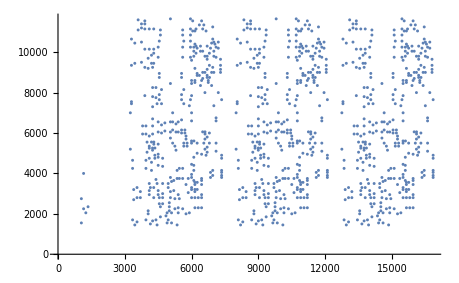

```mathematica
ListPlot[pts]
```

```mathematica
AbsoluteTiming[FindShortestTour[pts][[1]]]//N
```

{2.36777,258743.}

```mathematica
AbsoluteTiming[FindShortestTour[pts][[1]]]//N
```

{2.36265,258743.}

```mathematica
AbsoluteTiming[FindShortestTour[pts][[1]]]//N
```

{2.36078,258743.}

```mathematica
AbsoluteTiming[FindShortestTour[pts][[1]]]//N
```

{2.36163,258743.}

```mathematica
AbsoluteTiming[FindShortestTour[pts][[1]]]//N
```

{2.36023,258743.}

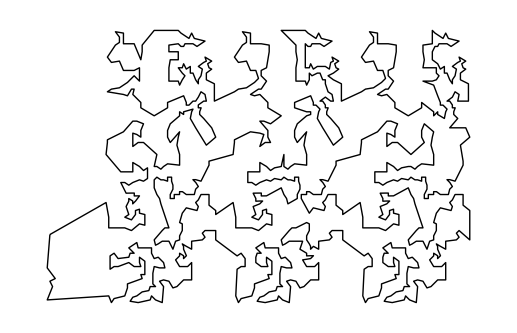

```mathematica
Graphics[Line[pts[[FindShortestTour[pts][[2]]]]]]
```

```mathematica
sol=Flatten[Drop[Import["/home/pi/Downloads/concorde/KDTREE/pr1002_boruvka","Table"],1]]+1;
```

```mathematica
sol=Append[sol,sol[[1]]]
```

{1,2,5,3,4,6,7,9,8,79,78,82,88,89,87,86,85,84,83,81,80,74,75,76,77,93,94,95,96,97,98,99,91,92,90,994,107,108,109,111,110,112,113,304,303,302,301,283,282,281,277,280,278,279,276,275,274,273,272,271,269,268,267,266,265,229,228,230,232,231,264,263,246,245,244,243,251,252,249,250,247,248,262,261,260,270,258,259,253,254,255,256,257,121,120,122,123,124,126,125,127,128,129,130,131,132,137,138,136,135,134,133,100,101,102,103,104,105,106,117,119,118,116,115,114,833,834,831,832,829,830,835,836,837,576,575,578,577,580,579,571,572,573,574,590,589,588,598,586,587,581,582,583,584,585,449,448,450,451,452,454,453,455,456,457,458,459,460,465,466,464,463,462,461,428,429,430,431,432,433,434,447,446,444,445,443,442,997,435,436,437,439,438,440,441,632,631,630,629,611,610,609,605,608,606,607,604,603,602,601,600,599,597,596,595,594,593,591,592,559,560,558,557,556,555,554,553,552,551,550,561,562,563,549,548,547,546,564,565,519,518,520,521,522,523,515,516,517,567,566,568,569,570,514,509,508,507,502,501,504,503,506,505,467,468,469,473,474,475,476,472,471,470,480,479,477,478,998,481,482,485,488,489,500,499,498,214,215,213,216,212,217,211,210,209,208,203,204,205,207,206,200,199,198,201,197,196,202,996,182,183,184,185,159,158,162,163,156,164,155,165,166,167,168,169,139,140,141,142,143,144,148,147,146,145,149,152,151,150,995,153,154,157,160,161,172,171,170,177,178,175,176,173,174,179,180,181,186,242,241,240,238,239,189,188,187,195,194,193,192,190,191,237,236,218,219,220,221,235,234,233,222,223,224,225,226,227,497,496,495,494,493,483,492,484,491,490,486,487,513,512,511,510,999,530,524,525,529,526,527,528,531,532,533,535,534,536,537,538,539,545,540,544,541,543,542,826,827,828,817,816,813,810,809,825,824,823,822,821,811,812,820,819,818,814,815,841,840,839,838,1002,858,852,853,857,854,855,856,859,860,861,862,863,864,865,866,867,873,868,872,869,870,871,876,875,874,892,893,847,846,848,845,844,849,850,851,843,842,898,897,896,894,895,889,890,891,877,878,879,880,881,882,883,905,906,903,904,918,917,916,926,914,915,909,910,911,912,913,777,776,778,779,780,782,781,783,784,785,786,787,788,793,794,792,791,790,789,756,757,758,759,760,761,762,775,774,772,773,771,770,768,766,767,769,960,959,958,957,939,938,937,933,936,934,935,932,931,930,929,928,927,925,924,923,922,921,885,884,886,888,887,920,919,902,901,900,899,907,908,1001,806,805,807,808,798,799,800,804,803,802,801,797,796,795,1000,763,764,765,730,731,732,733,749,750,751,752,753,754,755,747,748,746,741,742,743,745,744,738,734,735,736,737,739,740,702,703,704,705,707,716,717,721,715,714,722,723,712,711,713,709,708,710,727,729,728,724,725,726,663,665,664,671,673,672,669,670,666,667,668,718,720,719,688,689,690,691,692,693,694,695,696,706,697,698,699,700,701,968,967,966,965,964,963,962,961,993,953,954,956,955,940,941,942,943,944,945,946,947,948,952,951,949,950,977,978,979,976,975,974,973,969,972,971,970,987,986,985,984,983,980,981,982,990,989,988,684,683,685,686,687,682,681,680,679,678,677,674,675,676,348,347,346,349,350,351,352,353,354,359,358,357,355,356,660,661,662,654,653,652,655,656,657,658,659,642,643,644,641,645,646,647,648,651,650,649,622,621,623,624,620,619,618,617,616,615,614,613,612,627,628,626,625,992,633,634,635,636,637,638,639,640,373,372,371,370,369,378,368,367,366,365,364,363,362,361,360,391,392,390,340,339,338,342,341,344,345,343,336,337,335,398,397,396,400,401,399,382,380,381,385,383,384,395,394,386,387,393,389,388,379,377,376,375,374,418,420,419,427,426,425,424,423,422,421,405,404,403,402,408,409,411,412,413,414,415,417,416,410,406,407,296,295,293,294,292,291,290,289,288,287,286,285,284,299,300,298,297,991,305,306,307,308,309,310,311,312,45,44,43,42,41,50,40,39,38,37,36,35,34,33,32,63,64,62,60,61,65,59,58,66,67,56,55,57,53,52,54,51,49,48,47,46,313,316,315,314,331,330,329,328,327,326,325,324,319,320,318,317,321,322,323,334,333,332,28,27,29,30,31,26,25,24,23,22,21,18,19,20,15,17,16,13,14,10,11,12,70,69,68,72,73,71,1}

```mathematica
ArcLength[Line[pts[[sol]]]]
```

Part::partw: Part {1,2,5,3,4,6,7,9,8,79,78,82,88,89,87,86,85,84,83,81,80,74,75,76,77,93,94,95,96,97,98,99,91,92,90,994,107,108,109,111,110,112,113,304,303,302,301,283,282,281,«953»} of {{1150,4000},{1050,2750},{1150,2250},{1250,2050},{1350,2350},{1050,1550},{3350,1700},{3450,1450},{3550,1600},{3950,1700},{4050,2000},{4050,2150},{4250,1650},«25»,{5050,3100},{4950,3300},{5100,3600},{5200,3650},{5350,3750},{5450,3750},{5600,3750},{5600,4250},{5450,4250},{5350,4150},{5050,3800},{4950,3500},«951»} does not exist.

ArcLength::reg: Line[{{1150,4000},{1050,2750},{1150,2250},{1250,2050},{1350,2350},{1050,1550},{3350,1700},{3450,1450},{3550,1600},{3950,1700},{4050,2000},{4050,2150},{4250,1650},«26»,{4950,3300},{5100,3600},{5200,3650},{5350,3750},{5450,3750},{5600,3750},{5600,4250},{5450,4250},{5350,4150},{5050,3800},{4950,3500},«951»}⟦{«1»}⟧] is not a correctly specified region.

ArcLength[Line[{{1150,4000},{1050,2750},{1150,2250},{1250,2050},{1350,2350},{1050,1550},{3350,1700},{3450,1450},{3550,1600},{3950,1700},{4050,2000},{4050,2150},{4250,1650},{4150,1500},{4450,1450},{4400,1700},{4600,1850},{4900,1550},{5100,1550},{5350,1450},{4950,1700},{4850,1900},{4900,2050},{5000,2150},{5100,2050},{5400,2050},{5750,2000},{5900,2050},{5600,2250},{5400,2300},{5250,2250},{5000,2350},{5000,2550},{5050,2800},{5250,2750},{5450,2750},{5400,2950},{5200,3150},{5050,3100},{4950,3300},{5100,3600},{5200,3650},{5350,3750},{5450,3750},{5600,3750},{5600,4250},{5450,4250},{5350,4150},{5050,3800},{4950,3500},{4700,3500},{4400,3700},{4450,3500},{4100,3500},{4150,3300},{4100,3150},{4300,3300},{4500,3150},{4500,2950},{4700,3000},{4700,2800},{4700,2500},{4600,2350},{4550,2500},{4550,2800},{4300,2800},{4100,2950},{3700,2800},{3550,2800},{3400,2700},{3400,3200},{3700,3100},{3550,3300},{3350,4250},{3350,4650},{3250,5200},{4000,5050},{4100,4750},{3950,4650},{3950,4250},{4200,4150},{4200,4550},{4500,4400},{4700,4350},{4700,4750},{4500,4800},{4500,4950},{4350,4750},{4350,4900},{4247,5150},{4354,5256},{4247,5256},{4100,5250},{4100,5350},{4000,5550},{4199,5554},{4305,5554},{4304,5447},{4500,5450},{4500,6050},{4650,6000},{4800,6100},{5050,6050},{5150,6150},{5300,6050},{5400,6050},{5150,5500},{5250,5350},{5300,5150},{5650,5350},{5800,5350},{5650,5500},{5800,5500},{5750,5700},{5750,5850},{5700,6000},{5700,6150},{5550,6000},{5550,6150},{6000,6600},{6000,7000},{5550,6650},{5400,6550},{5300,6450},{5150,6550},{5150,7000},{5050,6550},{4800,6500},{4650,6400},{4500,6550},{4250,6700},{4250,6350},{4250,5950},{4100,5850},{3950,5950},{3800,5950},{3950,6350},{3800,6350},{3250,7000},{3300,7450},{3300,7550},{3900,7850},{4250,7800},{4400,7750},{4250,7300},{4450,7450},{4650,7450},{4550,7650},{4550,7900},{4650,8150},{4400,8250},{4250,8250},{4550,8750},{4550,8950},{4250,9250},{4300,9450},{4500,9750},{4300,9950},{4300,10150},{4100,10150},{3900,10150},{4200,9850},{4050,9700},{4200,9450},{4050,9200},{3900,9250},{3750,9500},{3450,9450},{3300,9350},{3300,10650},{3450,10450},{3750,10500},{3600,11100},{3750,11200},{3750,11400},{3600,11600},{3900,11550},{3900,11400},{3900,11150},{4100,11150},{4300,11150},{4600,11100},{4600,10850},{4550,10550},{4500,10250},{5600,9750},{5600,10250},{5950,10250},{6100,10250},{6250,10200},{6400,10300},{6200,10300},{6150,10400},{5950,10550},{5650,10550},{5600,10850},{5950,10850},{6050,11050},{6150,11050},{6200,11150},{5950,11150},{5600,11100},{5950,11650},{6050,11550},{6450,11550},{6350,11350},{6550,11350},{6500,11150},{6650,11050},{6950,11250},{6950,10650},{7000,10500},{7200,10500},{7200,10200},{7100,10250},{7050,10400},{6900,10450},{6700,10300},{6850,10200},{7000,10050},{6800,9950},{7000,9800},{7100,9750},{7300,9650},{7300,9350},{7300,9150},{7300,9000},{7000,9000},{6900,9000},{6950,9250},{6700,9150},{6800,9350},{6700,9650},{6700,9800},{6600,9800},{6500,10050},{6400,10050},{6200,9950},{6100,10050},{6100,9800},{5950,9750},{6000,9600},{6150,9200},{6250,8950},{6250,8850},{6350,8850},{6150,8600},{6150,8500},{6000,8450},{6000,8600},{5550,8950},{5550,8750},{5650,8150},{5550,7900},{5550,7650},{5650,7450},{5900,7350},{5950,7650},{6000,7850},{6400,8350},{6450,8600},{6500,8700},{6500,9000},{6600,9000},{6699,8856},{6699,8750},{6805,8749},{6750,8600},{6750,8500},{6600,8000},{6900,8350},{7200,8000},{7350,7650},{7000,7350},{7100,6750},{7100,6600},{6800,6000},{6603,6057},{6498,6057},{6604,5950},{6700,5800},{6600,5700},{6550,5500},{6800,5500},{7100,5500},{7100,5100},{7350,4900},{7350,4750},{7350,4150},{7350,4050},{7350,3900},{7350,3800},{6950,3900},{6850,3800},{6850,4050},{6950,4150},{6650,4900},{6700,5050},{6700,5300},{6600,5200},{6250,5500},{6106,5606},{5999,5607},{5998,5500},{6250,5000},{6100,4800},{6000,4450},{6100,4400},{6100,4150},{6000,3950},{6000,3800},{5850,3750},{5750,3450},{5850,3050},{6000,3200},{6000,3300},{6100,3650},{6148,3556},{6148,3450},{6254,3557},{6450,3750},{6450,3650},{6450,3450},{6254,3206},{6148,3206},{6148,3099},{6450,2950},{6450,2800},{6300,2800},{6150,2800},{6000,2800},{6150,2300},{6300,2300},{6450,2300},{8100,1700},{8200,1450},{8300,1600},{8700,1700},{8800,2000},{8800,2150},{9000,1650},{8900,1500},{9200,1450},{9150,1700},{9350,1850},{9650,1550},{9850,1550},{10100,1450},{9700,1700},{9600,1900},{9650,2050},{9750,2150},{9850,2050},{10150,2050},{10500,2000},{10650,2050},{10350,2250},{10150,2300},{10000,2250},{9750,2350},{9750,2550},{9800,2800},{10000,2750},{10200,2750},{10150,2950},{9950,3150},{9800,3100},{9700,3300},{9850,3600},{9950,3650},{10100,3750},{10200,3750},{10350,3750},{10350,4250},{10200,4250},{10100,4150},{9800,3800},{9700,3500},{9450,3500},{9150,3700},{9200,3500},{8850,3500},{8900,3300},{8850,3150},{9050,3300},{9250,3150},{9250,2950},{9450,3000},{9450,2800},{9450,2500},{9350,2350},{9300,2500},{9300,2800},{9050,2800},{8850,2950},{8450,2800},{8300,2800},{8150,2700},{8150,3200},{8450,3100},{8300,3300},{8100,4250},{8100,4650},{8000,5200},{8750,5050},{8850,4750},{8700,4650},{8700,4250},{8950,4150},{8950,4550},{9250,4400},{9450,4350},{9450,4750},{9250,4800},{9250,4950},{9100,4750},{9100,4900},{8997,5150},{9104,5256},{8997,5256},{8850,5250},{8850,5350},{8750,5550},{8949,5554},{9055,5554},{9054,5447},{9250,5450},{9250,6050},{9400,6000},{9550,6100},{9800,6050},{9900,6150},{10050,6050},{10150,6050},{9900,5500},{10000,5350},{10050,5150},{10400,5350},{10550,5350},{10400,5500},{10550,5500},{10500,5700},{10500,5850},{10450,6000},{10450,6150},{10300,6000},{10300,6150},{10750,6600},{10750,7000},{10300,6650},{10150,6550},{10050,6450},{9900,6550},{9900,7000},{9800,6550},{9550,6500},{9400,6400},{9250,6550},{9000,6700},{9000,6350},{9000,5950},{8850,5850},{8700,5950},{8550,5950},{8700,6350},{8550,6350},{8000,7000},{8050,7450},{8050,7550},{8650,7850},{9000,7800},{9150,7750},{9000,7300},{9200,7450},{9400,7450},{9300,7650},{9300,7900},{9400,8150},{9150,8250},{9000,8250},{9300,8750},{9300,8950},{9000,9250},{9050,9450},{9250,9750},{9050,9950},{9050,10150},{8850,10150},{8650,10150},{8950,9850},{8800,9700},{8950,9450},{8800,9200},{8650,9250},{8500,9500},{8200,9450},{8050,9350},{8050,10650},{8200,10450},{8500,10500},{8350,11100},{8500,11200},{8500,11400},{8350,11600},{8650,11550},{8650,11400},{8650,11150},{8850,11150},{9050,11150},{9350,11100},{9350,10850},{9300,10550},{9250,10250},{10350,9750},{10350,10250},{10700,10250},{10850,10250},{11000,10200},{11150,10300},{10950,10300},{10900,10400},{10700,10550},{10400,10550},{10350,10850},{10700,10850},{10800,11050},{10900,11050},{10950,11150},{10700,11150},{10350,11100},{10700,11650},{10800,11550},{11200,11550},{11100,11350},{11300,11350},{11250,11150},{11400,11050},{11700,11250},{11700,10650},{11750,10500},{11950,10500},{11950,10200},{11850,10250},{11800,10400},{11650,10450},{11450,10300},{11600,10200},{11750,10050},{11550,9950},{11750,9800},{11850,9750},{12050,9650},{12050,9350},{12050,9150},{12050,9000},{11750,9000},{11650,9000},{11700,9250},{11450,9150},{11550,9350},{11450,9650},{11450,9800},{11350,9800},{11250,10050},{11150,10050},{10950,9950},{10850,10050},{10850,9800},{10700,9750},{10750,9600},{10900,9200},{11000,8950},{11000,8850},{11100,8850},{10900,8600},{10900,8500},{10750,8450},{10750,8600},{10300,8950},{10300,8750},{10400,8150},{10300,7900},{10300,7650},{10400,7450},{10650,7350},{10700,7650},{10750,7850},{11150,8350},{11200,8600},{11250,8700},{11250,9000},{11350,9000},{11449,8856},{11449,8750},{11555,8749},{11500,8600},{11500,8500},{11350,8000},{11650,8350},{11950,8000},{12100,7650},{11750,7350},{11850,6750},{11850,6600},{11550,6000},{11353,6057},{11248,6057},{11354,5950},{11450,5800},{11350,5700},{11300,5500},{11550,5500},{11850,5500},{11850,5100},{12100,4900},{12100,4750},{12100,4150},{12100,4050},{12100,3900},{12100,3800},{11700,3900},{11600,3800},{11600,4050},{11700,4150},{11400,4900},{11450,5050},{11450,5300},{11350,5200},{11000,5500},{10856,5606},{10749,5607},{10748,5500},{11000,5000},{10850,4800},{10750,4450},{10850,4400},{10850,4150},{10750,3950},{10750,3800},{10600,3750},{10500,3450},{10600,3050},{10750,3200},{10750,3300},{10850,3650},{10898,3556},{10898,3450},{11004,3557},{11200,3750},{11200,3650},{11200,3450},{11004,3206},{10898,3206},{10898,3099},{11200,2950},{11200,2800},{11050,2800},{10900,2800},{10750,2800},{10900,2300},{11050,2300},{11200,2300},{12850,1700},{12950,1450},{13050,1600},{13450,1700},{13550,2000},{13550,2150},{13750,1650},{13650,1500},{13950,1450},{13900,1700},{14100,1850},{14400,1550},{14600,1550},{14850,1450},{14450,1700},{14350,1900},{14400,2050},{14500,2150},{14600,2050},{14900,2050},{15250,2000},{15400,2050},{15100,2250},{14900,2300},{14750,2250},{14500,2350},{14500,2550},{14550,2800},{14750,2750},{14950,2750},{14900,2950},{14700,3150},{14550,3100},{14450,3300},{14600,3600},{14700,3650},{14850,3750},{14950,3750},{15100,3750},{15100,4250},{14950,4250},{14850,4150},{14550,3800},{14450,3500},{14200,3500},{13900,3700},{13950,3500},{13600,3500},{13650,3300},{13600,3150},{13800,3300},{14000,3150},{14000,2950},{14200,3000},{14200,2800},{14200,2500},{14100,2350},{14050,2500},{14050,2800},{13800,2800},{13600,2950},{13200,2800},{13050,2800},{12900,2700},{12900,3200},{13200,3100},{13050,3300},{12850,4250},{12850,4650},{12750,5200},{13500,5050},{13600,4750},{13450,4650},{13450,4250},{13700,4150},{13700,4550},{14000,4400},{14200,4350},{14200,4750},{14000,4800},{14000,4950},{13850,4750},{13850,4900},{13747,5150},{13854,5256},{13747,5256},{13600,5250},{13600,5350},{13500,5550},{13699,5554},{13805,5554},{13804,5447},{14000,5450},{14000,6050},{14150,6000},{14300,6100},{14550,6050},{14650,6150},{14800,6050},{14900,6050},{14650,5500},{14750,5350},{14800,5150},{15150,5350},{15300,5350},{15150,5500},{15300,5500},{15250,5700},{15250,5850},{15200,6000},{15200,6150},{15050,6000},{15050,6150},{15500,6600},{15500,7000},{15050,6650},{14900,6550},{14800,6450},{14650,6550},{14650,7000},{14550,6550},{14300,6500},{14150,6400},{14000,6550},{13750,6700},{13750,6350},{13750,5950},{13600,5850},{13450,5950},{13300,5950},{13450,6350},{13300,6350},{12750,7000},{12800,7450},{12800,7550},{13400,7850},{13750,7800},{13900,7750},{13750,7300},{13950,7450},{14150,7450},{14050,7650},{14050,7900},{14150,8150},{13900,8250},{13750,8250},{14050,8750},{14050,8950},{13750,9250},{13800,9450},{14000,9750},{13800,9950},{13800,10150},{13600,10150},{13400,10150},{13700,9850},{13550,9700},{13700,9450},{13550,9200},{13400,9250},{13250,9500},{12950,9450},{12800,9350},{12800,10650},{12950,10450},{13250,10500},{13100,11100},{13250,11200},{13250,11400},{13100,11600},{13400,11550},{13400,11400},{13400,11150},{13600,11150},{13800,11150},{14100,11100},{14100,10850},{14050,10550},{14000,10250},{15100,9750},{15100,10250},{15450,10250},{15600,10250},{15750,10200},{15900,10300},{15700,10300},{15650,10400},{15450,10550},{15150,10550},{15100,10850},{15450,10850},{15550,11050},{15650,11050},{15700,11150},{15450,11150},{15100,11100},{15450,11650},{15550,11550},{15950,11550},{15850,11350},{16050,11350},{16000,11150},{16150,11050},{16450,11250},{16450,10650},{16500,10500},{16700,10500},{16700,10200},{16600,10250},{16550,10400},{16400,10450},{16200,10300},{16350,10200},{16500,10050},{16300,9950},{16500,9800},{16600,9750},{16800,9650},{16800,9350},{16800,9150},{16800,9000},{16500,9000},{16400,9000},{16450,9250},{16200,9150},{16300,9350},{16200,9650},{16200,9800},{16100,9800},{16000,10050},{15900,10050},{15700,9950},{15600,10050},{15600,9800},{15450,9750},{15500,9600},{15650,9200},{15750,8950},{15750,8850},{15850,8850},{15650,8600},{15650,8500},{15500,8450},{15500,8600},{15050,8950},{15050,8750},{15150,8150},{15050,7900},{15050,7650},{15150,7450},{15400,7350},{15450,7650},{15500,7850},{15900,8350},{15950,8600},{16000,8700},{16000,9000},{16100,9000},{16199,8856},{16199,8750},{16305,8749},{16250,8600},{16250,8500},{16100,8000},{16400,8350},{16700,8000},{16850,7650},{16500,7350},{16600,6750},{16600,6600},{16300,6000},{16103,6057},{15998,6057},{16104,5950},{16200,5800},{16100,5700},{16050,5500},{16300,5500},{16600,5500},{16600,5100},{16850,4900},{16850,4750},{16850,4150},{16850,4050},{16850,3900},{16850,3800},{16450,3900},{16350,3800},{16350,4050},{16450,4150},{16150,4900},{16200,5050},{16200,5300},{16100,5200},{15750,5500},{15606,5606},{15499,5607},{15498,5500},{15750,5000},{15600,4800},{15500,4450},{15600,4400},{15600,4150},{15500,3950},{15500,3800},{15350,3750},{15250,3450},{15350,3050},{15500,3200},{15500,3300},{15600,3650},{15648,3556},{15648,3450},{15754,3557},{15950,3750},{15950,3650},{15950,3450},{15754,3206},{15648,3206},{15648,3099},{15950,2950},{15950,2800},{15800,2800},{15650,2800},{15500,2800},{15650,2300},{15800,2300},{15950,2300},{6450,4950},{11200,4950},{15950,4950},{5050,5750},{5050,8450},{5050,11650},{9800,5750},{9800,8450},{9800,11650},{14550,5750},{14550,8450}}⟦{1,2,5,3,4,6,7,9,8,79,78,82,88,89,87,86,85,84,83,81,80,74,75,76,77,93,94,95,96,97,98,99,91,92,90,994,107,108,109,111,110,112,113,304,303,302,301,283,282,281,277,280,278,279,276,275,274,273,272,271,269,268,267,266,265,229,228,230,232,231,264,263,246,245,244,243,251,252,249,250,247,248,262,261,260,270,258,259,253,254,255,256,257,121,120,122,123,124,126,125,127,128,129,130,131,132,137,138,136,135,134,133,100,101,102,103,104,105,106,117,119,118,116,115,114,833,834,831,832,829,830,835,836,837,576,575,578,577,580,579,571,572,573,574,590,589,588,598,586,587,581,582,583,584,585,449,448,450,451,452,454,453,455,456,457,458,459,460,465,466,464,463,462,461,428,429,430,431,432,433,434,447,446,444,445,443,442,997,435,436,437,439,438,440,441,632,631,630,629,611,610,609,605,608,606,607,604,603,602,601,600,599,597,596,595,594,593,591,592,559,560,558,557,556,555,554,553,552,551,550,561,562,563,549,548,547,546,564,565,519,518,520,521,522,523,515,516,517,567,566,568,569,570,514,509,508,507,502,501,504,503,506,505,467,468,469,473,474,475,476,472,471,470,480,479,477,478,998,481,482,485,488,489,500,499,498,214,215,213,216,212,217,211,210,209,208,203,204,205,207,206,200,199,198,201,197,196,202,996,182,183,184,185,159,158,162,163,156,164,155,165,166,167,168,169,139,140,141,142,143,144,148,147,146,145,149,152,151,150,995,153,154,157,160,161,172,171,170,177,178,175,176,173,174,179,180,181,186,242,241,240,238,239,189,188,187,195,194,193,192,190,191,237,236,218,219,220,221,235,234,233,222,223,224,225,226,227,497,496,495,494,493,483,492,484,491,490,486,487,513,512,511,510,999,530,524,525,529,526,527,528,531,532,533,535,534,536,537,538,539,545,540,544,541,543,542,826,827,828,817,816,813,810,809,825,824,823,822,821,811,812,820,819,818,814,815,841,840,839,838,1002,858,852,853,857,854,855,856,859,860,861,862,863,864,865,866,867,873,868,872,869,870,871,876,875,874,892,893,847,846,848,845,844,849,850,851,843,842,898,897,896,894,895,889,890,891,877,878,879,880,881,882,883,905,906,903,904,918,917,916,926,914,915,909,910,911,912,913,777,776,778,779,780,782,781,783,784,785,786,787,788,793,794,792,791,790,789,756,757,758,759,760,761,762,775,774,772,773,771,770,768,766,767,769,960,959,958,957,939,938,937,933,936,934,935,932,931,930,929,928,927,925,924,923,922,921,885,884,886,888,887,920,919,902,901,900,899,907,908,1001,806,805,807,808,798,799,800,804,803,802,801,797,796,795,1000,763,764,765,730,731,732,733,749,750,751,752,753,754,755,747,748,746,741,742,743,745,744,738,734,735,736,737,739,740,702,703,704,705,707,716,717,721,715,714,722,723,712,711,713,709,708,710,727,729,728,724,725,726,663,665,664,671,673,672,669,670,666,667,668,718,720,719,688,689,690,691,692,693,694,695,696,706,697,698,699,700,701,968,967,966,965,964,963,962,961,993,953,954,956,955,940,941,942,943,944,945,946,947,948,952,951,949,950,977,978,979,976,975,974,973,969,972,971,970,987,986,985,984,983,980,981,982,990,989,988,684,683,685,686,687,682,681,680,679,678,677,674,675,676,348,347,346,349,350,351,352,353,354,359,358,357,355,356,660,661,662,654,653,652,655,656,657,658,659,642,643,644,641,645,646,647,648,651,650,649,622,621,623,624,620,619,618,617,616,615,614,613,612,627,628,626,625,992,633,634,635,636,637,638,639,640,373,372,371,370,369,378,368,367,366,365,364,363,362,361,360,391,392,390,340,339,338,342,341,344,345,343,336,337,335,398,397,396,400,401,399,382,380,381,385,383,384,395,394,386,387,393,389,388,379,377,376,375,374,418,420,419,427,426,425,424,423,422,421,405,404,403,402,408,409,411,412,413,414,415,417,416,410,406,407,296,295,293,294,292,291,290,289,288,287,286,285,284,299,300,298,297,991,305,306,307,308,309,310,311,312,45,44,43,42,41,50,40,39,38,37,36,35,34,33,32,63,64,62,60,61,65,59,58,66,67,56,55,57,53,52,54,51,49,48,47,46,313,316,315,314,331,330,329,328,327,326,325,324,319,320,318,317,321,322,323,334,333,332,28,27,29,30,31,26,25,24,23,22,21,18,19,20,15,17,16,13,14,10,11,12,70,69,68,72,73,71,1}⟧]]

```mathematica
SolIn["/home/pi/Downloads/concorde/KDTREE/pr1002_boruvka"][[1]]
```

Part::partw: Part {1,2,5,3,4,6,7,9,8,79,78,82,88,89,87,86,85,84,83,81,80,74,75,76,77,93,94,95,96,97,98,99,91,92,90,994,107,108,109,111,110,112,113,304,303,302,301,283,282,281,«953»} of {{1150,4000},{1050,2750},{1150,2250},{1250,2050},{1350,2350},{1050,1550},{3350,1700},{3450,1450},{3550,1600},{3950,1700},{4050,2000},{4050,2150},{4250,1650},«25»,{5050,3100},{4950,3300},{5100,3600},{5200,3650},{5350,3750},{5450,3750},{5600,3750},{5600,4250},{5450,4250},{5350,4150},{5050,3800},{4950,3500},«951»} does not exist.

ArcLength::reg: Line[{{1150,4000},{1050,2750},{1150,2250},{1250,2050},{1350,2350},{1050,1550},{3350,1700},{3450,1450},{3550,1600},{3950,1700},{4050,2000},{4050,2150},{4250,1650},«26»,{4950,3300},{5100,3600},{5200,3650},{5350,3750},{5450,3750},{5600,3750},{5600,4250},{5450,4250},{5350,4150},{5050,3800},{4950,3500},«951»}⟦{«1»}⟧] is not a correctly specified region.

Part::partw: Part {1,2,5,3,4,6,7,9,8,79,78,82,88,89,87,86,85,84,83,81,80,74,75,76,77,93,94,95,96,97,98,99,91,92,90,994,107,108,109,111,110,112,113,304,303,302,301,283,282,281,«953»} of {{1150.,4000.},{1050.,2750.},{1150.,2250.},{1250.,2050.},{1350.,2350.},{1050.,1550.},{3350.,1700.},{3450.,1450.},{3550.,1600.},{3950.,1700.},«31»,{5200.,3650.},{5350.,3750.},{5450.,3750.},{5600.,3750.},{5600.,4250.},{5450.,4250.},{5350.,4150.},{5050.,3800.},{4950.,3500.},«951»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ArcLength::reg: Line[{{1150.,4000.},{1050.,2750.},{1150.,2250.},{1250.,2050.},{1350.,2350.},{1050.,1550.},{3350.,1700.},{3450.,1450.},{3550.,1600.},«33»,{5350.,3750.},{5450.,3750.},{5600.,3750.},{5600.,4250.},{5450.,4250.},{5350.,4150.},{5050.,3800.},{4950.,3500.},«951»}⟦{1,2,5,«46»,281,«953»}⟧] is not a correctly specified region.

ArcLength[Line[{{1150.,4000.},{1050.,2750.},{1150.,2250.},{1250.,2050.},{1350.,2350.},{1050.,1550.},{3350.,1700.},{3450.,1450.},{3550.,1600.},{3950.,1700.},{4050.,2000.},{4050.,2150.},{4250.,1650.},{4150.,1500.},{4450.,1450.},{4400.,1700.},{4600.,1850.},{4900.,1550.},{5100.,1550.},{5350.,1450.},{4950.,1700.},{4850.,1900.},{4900.,2050.},{5000.,2150.},{5100.,2050.},{5400.,2050.},{5750.,2000.},{5900.,2050.},{5600.,2250.},{5400.,2300.},{5250.,2250.},{5000.,2350.},{5000.,2550.},{5050.,2800.},{5250.,2750.},{5450.,2750.},{5400.,2950.},{5200.,3150.},{5050.,3100.},{4950.,3300.},{5100.,3600.},{5200.,3650.},{5350.,3750.},{5450.,3750.},{5600.,3750.},{5600.,4250.},{5450.,4250.},{5350.,4150.},{5050.,3800.},{4950.,3500.},{4700.,3500.},{4400.,3700.},{4450.,3500.},{4100.,3500.},{4150.,3300.},{4100.,3150.},{4300.,3300.},{4500.,3150.},{4500.,2950.},{4700.,3000.},{4700.,2800.},{4700.,2500.},{4600.,2350.},{4550.,2500.},{4550.,2800.},{4300.,2800.},{4100.,2950.},{3700.,2800.},{3550.,2800.},{3400.,2700.},{3400.,3200.},{3700.,3100.},{3550.,3300.},{3350.,4250.},{3350.,4650.},{3250.,5200.},{4000.,5050.},{4100.,4750.},{3950.,4650.},{3950.,4250.},{4200.,4150.},{4200.,4550.},{4500.,4400.},{4700.,4350.},{4700.,4750.},{4500.,4800.},{4500.,4950.},{4350.,4750.},{4350.,4900.},{4247.,5150.},{4354.,5256.},{4247.,5256.},{4100.,5250.},{4100.,5350.},{4000.,5550.},{4199.,5554.},{4305.,5554.},{4304.,5447.},{4500.,5450.},{4500.,6050.},{4650.,6000.},{4800.,6100.},{5050.,6050.},{5150.,6150.},{5300.,6050.},{5400.,6050.},{5150.,5500.},{5250.,5350.},{5300.,5150.},{5650.,5350.},{5800.,5350.},{5650.,5500.},{5800.,5500.},{5750.,5700.},{5750.,5850.},{5700.,6000.},{5700.,6150.},{5550.,6000.},{5550.,6150.},{6000.,6600.},{6000.,7000.},{5550.,6650.},{5400.,6550.},{5300.,6450.},{5150.,6550.},{5150.,7000.},{5050.,6550.},{4800.,6500.},{4650.,6400.},{4500.,6550.},{4250.,6700.},{4250.,6350.},{4250.,5950.},{4100.,5850.},{3950.,5950.},{3800.,5950.},{3950.,6350.},{3800.,6350.},{3250.,7000.},{3300.,7450.},{3300.,7550.},{3900.,7850.},{4250.,7800.},{4400.,7750.},{4250.,7300.},{4450.,7450.},{4650.,7450.},{4550.,7650.},{4550.,7900.},{4650.,8150.},{4400.,8250.},{4250.,8250.},{4550.,8750.},{4550.,8950.},{4250.,9250.},{4300.,9450.},{4500.,9750.},{4300.,9950.},{4300.,10150.},{4100.,10150.},{3900.,10150.},{4200.,9850.},{4050.,9700.},{4200.,9450.},{4050.,9200.},{3900.,9250.},{3750.,9500.},{3450.,9450.},{3300.,9350.},{3300.,10650.},{3450.,10450.},{3750.,10500.},{3600.,11100.},{3750.,11200.},{3750.,11400.},{3600.,11600.},{3900.,11550.},{3900.,11400.},{3900.,11150.},{4100.,11150.},{4300.,11150.},{4600.,11100.},{4600.,10850.},{4550.,10550.},{4500.,10250.},{5600.,9750.},{5600.,10250.},{5950.,10250.},{6100.,10250.},{6250.,10200.},{6400.,10300.},{6200.,10300.},{6150.,10400.},{5950.,10550.},{5650.,10550.},{5600.,10850.},{5950.,10850.},{6050.,11050.},{6150.,11050.},{6200.,11150.},{5950.,11150.},{5600.,11100.},{5950.,11650.},{6050.,11550.},{6450.,11550.},{6350.,11350.},{6550.,11350.},{6500.,11150.},{6650.,11050.},{6950.,11250.},{6950.,10650.},{7000.,10500.},{7200.,10500.},{7200.,10200.},{7100.,10250.},{7050.,10400.},{6900.,10450.},{6700.,10300.},{6850.,10200.},{7000.,10050.},{6800.,9950.},{7000.,9800.},{7100.,9750.},{7300.,9650.},{7300.,9350.},{7300.,9150.},{7300.,9000.},{7000.,9000.},{6900.,9000.},{6950.,9250.},{6700.,9150.},{6800.,9350.},{6700.,9650.},{6700.,9800.},{6600.,9800.},{6500.,10050.},{6400.,10050.},{6200.,9950.},{6100.,10050.},{6100.,9800.},{5950.,9750.},{6000.,9600.},{6150.,9200.},{6250.,8950.},{6250.,8850.},{6350.,8850.},{6150.,8600.},{6150.,8500.},{6000.,8450.},{6000.,8600.},{5550.,8950.},{5550.,8750.},{5650.,8150.},{5550.,7900.},{5550.,7650.},{5650.,7450.},{5900.,7350.},{5950.,7650.},{6000.,7850.},{6400.,8350.},{6450.,8600.},{6500.,8700.},{6500.,9000.},{6600.,9000.},{6699.,8856.},{6699.,8750.},{6805.,8749.},{6750.,8600.},{6750.,8500.},{6600.,8000.},{6900.,8350.},{7200.,8000.},{7350.,7650.},{7000.,7350.},{7100.,6750.},{7100.,6600.},{6800.,6000.},{6603.,6057.},{6498.,6057.},{6604.,5950.},{6700.,5800.},{6600.,5700.},{6550.,5500.},{6800.,5500.},{7100.,5500.},{7100.,5100.},{7350.,4900.},{7350.,4750.},{7350.,4150.},{7350.,4050.},{7350.,3900.},{7350.,3800.},{6950.,3900.},{6850.,3800.},{6850.,4050.},{6950.,4150.},{6650.,4900.},{6700.,5050.},{6700.,5300.},{6600.,5200.},{6250.,5500.},{6106.,5606.},{5999.,5607.},{5998.,5500.},{6250.,5000.},{6100.,4800.},{6000.,4450.},{6100.,4400.},{6100.,4150.},{6000.,3950.},{6000.,3800.},{5850.,3750.},{5750.,3450.},{5850.,3050.},{6000.,3200.},{6000.,3300.},{6100.,3650.},{6148.,3556.},{6148.,3450.},{6254.,3557.},{6450.,3750.},{6450.,3650.},{6450.,3450.},{6254.,3206.},{6148.,3206.},{6148.,3099.},{6450.,2950.},{6450.,2800.},{6300.,2800.},{6150.,2800.},{6000.,2800.},{6150.,2300.},{6300.,2300.},{6450.,2300.},{8100.,1700.},{8200.,1450.},{8300.,1600.},{8700.,1700.},{8800.,2000.},{8800.,2150.},{9000.,1650.},{8900.,1500.},{9200.,1450.},{9150.,1700.},{9350.,1850.},{9650.,1550.},{9850.,1550.},{10100.,1450.},{9700.,1700.},{9600.,1900.},{9650.,2050.},{9750.,2150.},{9850.,2050.},{10150.,2050.},{10500.,2000.},{10650.,2050.},{10350.,2250.},{10150.,2300.},{10000.,2250.},{9750.,2350.},{9750.,2550.},{9800.,2800.},{10000.,2750.},{10200.,2750.},{10150.,2950.},{9950.,3150.},{9800.,3100.},{9700.,3300.},{9850.,3600.},{9950.,3650.},{10100.,3750.},{10200.,3750.},{10350.,3750.},{10350.,4250.},{10200.,4250.},{10100.,4150.},{9800.,3800.},{9700.,3500.},{9450.,3500.},{9150.,3700.},{9200.,3500.},{8850.,3500.},{8900.,3300.},{8850.,3150.},{9050.,3300.},{9250.,3150.},{9250.,2950.},{9450.,3000.},{9450.,2800.},{9450.,2500.},{9350.,2350.},{9300.,2500.},{9300.,2800.},{9050.,2800.},{8850.,2950.},{8450.,2800.},{8300.,2800.},{8150.,2700.},{8150.,3200.},{8450.,3100.},{8300.,3300.},{8100.,4250.},{8100.,4650.},{8000.,5200.},{8750.,5050.},{8850.,4750.},{8700.,4650.},{8700.,4250.},{8950.,4150.},{8950.,4550.},{9250.,4400.},{9450.,4350.},{9450.,4750.},{9250.,4800.},{9250.,4950.},{9100.,4750.},{9100.,4900.},{8997.,5150.},{9104.,5256.},{8997.,5256.},{8850.,5250.},{8850.,5350.},{8750.,5550.},{8949.,5554.},{9055.,5554.},{9054.,5447.},{9250.,5450.},{9250.,6050.},{9400.,6000.},{9550.,6100.},{9800.,6050.},{9900.,6150.},{10050.,6050.},{10150.,6050.},{9900.,5500.},{10000.,5350.},{10050.,5150.},{10400.,5350.},{10550.,5350.},{10400.,5500.},{10550.,5500.},{10500.,5700.},{10500.,5850.},{10450.,6000.},{10450.,6150.},{10300.,6000.},{10300.,6150.},{10750.,6600.},{10750.,7000.},{10300.,6650.},{10150.,6550.},{10050.,6450.},{9900.,6550.},{9900.,7000.},{9800.,6550.},{9550.,6500.},{9400.,6400.},{9250.,6550.},{9000.,6700.},{9000.,6350.},{9000.,5950.},{8850.,5850.},{8700.,5950.},{8550.,5950.},{8700.,6350.},{8550.,6350.},{8000.,7000.},{8050.,7450.},{8050.,7550.},{8650.,7850.},{9000.,7800.},{9150.,7750.},{9000.,7300.},{9200.,7450.},{9400.,7450.},{9300.,7650.},{9300.,7900.},{9400.,8150.},{9150.,8250.},{9000.,8250.},{9300.,8750.},{9300.,8950.},{9000.,9250.},{9050.,9450.},{9250.,9750.},{9050.,9950.},{9050.,10150.},{8850.,10150.},{8650.,10150.},{8950.,9850.},{8800.,9700.},{8950.,9450.},{8800.,9200.},{8650.,9250.},{8500.,9500.},{8200.,9450.},{8050.,9350.},{8050.,10650.},{8200.,10450.},{8500.,10500.},{8350.,11100.},{8500.,11200.},{8500.,11400.},{8350.,11600.},{8650.,11550.},{8650.,11400.},{8650.,11150.},{8850.,11150.},{9050.,11150.},{9350.,11100.},{9350.,10850.},{9300.,10550.},{9250.,10250.},{10350.,9750.},{10350.,10250.},{10700.,10250.},{10850.,10250.},{11000.,10200.},{11150.,10300.},{10950.,10300.},{10900.,10400.},{10700.,10550.},{10400.,10550.},{10350.,10850.},{10700.,10850.},{10800.,11050.},{10900.,11050.},{10950.,11150.},{10700.,11150.},{10350.,11100.},{10700.,11650.},{10800.,11550.},{11200.,11550.},{11100.,11350.},{11300.,11350.},{11250.,11150.},{11400.,11050.},{11700.,11250.},{11700.,10650.},{11750.,10500.},{11950.,10500.},{11950.,10200.},{11850.,10250.},{11800.,10400.},{11650.,10450.},{11450.,10300.},{11600.,10200.},{11750.,10050.},{11550.,9950.},{11750.,9800.},{11850.,9750.},{12050.,9650.},{12050.,9350.},{12050.,9150.},{12050.,9000.},{11750.,9000.},{11650.,9000.},{11700.,9250.},{11450.,9150.},{11550.,9350.},{11450.,9650.},{11450.,9800.},{11350.,9800.},{11250.,10050.},{11150.,10050.},{10950.,9950.},{10850.,10050.},{10850.,9800.},{10700.,9750.},{10750.,9600.},{10900.,9200.},{11000.,8950.},{11000.,8850.},{11100.,8850.},{10900.,8600.},{10900.,8500.},{10750.,8450.},{10750.,8600.},{10300.,8950.},{10300.,8750.},{10400.,8150.},{10300.,7900.},{10300.,7650.},{10400.,7450.},{10650.,7350.},{10700.,7650.},{10750.,7850.},{11150.,8350.},{11200.,8600.},{11250.,8700.},{11250.,9000.},{11350.,9000.},{11449.,8856.},{11449.,8750.},{11555.,8749.},{11500.,8600.},{11500.,8500.},{11350.,8000.},{11650.,8350.},{11950.,8000.},{12100.,7650.},{11750.,7350.},{11850.,6750.},{11850.,6600.},{11550.,6000.},{11353.,6057.},{11248.,6057.},{11354.,5950.},{11450.,5800.},{11350.,5700.},{11300.,5500.},{11550.,5500.},{11850.,5500.},{11850.,5100.},{12100.,4900.},{12100.,4750.},{12100.,4150.},{12100.,4050.},{12100.,3900.},{12100.,3800.},{11700.,3900.},{11600.,3800.},{11600.,4050.},{11700.,4150.},{11400.,4900.},{11450.,5050.},{11450.,5300.},{11350.,5200.},{11000.,5500.},{10856.,5606.},{10749.,5607.},{10748.,5500.},{11000.,5000.},{10850.,4800.},{10750.,4450.},{10850.,4400.},{10850.,4150.},{10750.,3950.},{10750.,3800.},{10600.,3750.},{10500.,3450.},{10600.,3050.},{10750.,3200.},{10750.,3300.},{10850.,3650.},{10898.,3556.},{10898.,3450.},{11004.,3557.},{11200.,3750.},{11200.,3650.},{11200.,3450.},{11004.,3206.},{10898.,3206.},{10898.,3099.},{11200.,2950.},{11200.,2800.},{11050.,2800.},{10900.,2800.},{10750.,2800.},{10900.,2300.},{11050.,2300.},{11200.,2300.},{12850.,1700.},{12950.,1450.},{13050.,1600.},{13450.,1700.},{13550.,2000.},{13550.,2150.},{13750.,1650.},{13650.,1500.},{13950.,1450.},{13900.,1700.},{14100.,1850.},{14400.,1550.},{14600.,1550.},{14850.,1450.},{14450.,1700.},{14350.,1900.},{14400.,2050.},{14500.,2150.},{14600.,2050.},{14900.,2050.},{15250.,2000.},{15400.,2050.},{15100.,2250.},{14900.,2300.},{14750.,2250.},{14500.,2350.},{14500.,2550.},{14550.,2800.},{14750.,2750.},{14950.,2750.},{14900.,2950.},{14700.,3150.},{14550.,3100.},{14450.,3300.},{14600.,3600.},{14700.,3650.},{14850.,3750.},{14950.,3750.},{15100.,3750.},{15100.,4250.},{14950.,4250.},{14850.,4150.},{14550.,3800.},{14450.,3500.},{14200.,3500.},{13900.,3700.},{13950.,3500.},{13600.,3500.},{13650.,3300.},{13600.,3150.},{13800.,3300.},{14000.,3150.},{14000.,2950.},{14200.,3000.},{14200.,2800.},{14200.,2500.},{14100.,2350.},{14050.,2500.},{14050.,2800.},{13800.,2800.},{13600.,2950.},{13200.,2800.},{13050.,2800.},{12900.,2700.},{12900.,3200.},{13200.,3100.},{13050.,3300.},{12850.,4250.},{12850.,4650.},{12750.,5200.},{13500.,5050.},{13600.,4750.},{13450.,4650.},{13450.,4250.},{13700.,4150.},{13700.,4550.},{14000.,4400.},{14200.,4350.},{14200.,4750.},{14000.,4800.},{14000.,4950.},{13850.,4750.},{13850.,4900.},{13747.,5150.},{13854.,5256.},{13747.,5256.},{13600.,5250.},{13600.,5350.},{13500.,5550.},{13699.,5554.},{13805.,5554.},{13804.,5447.},{14000.,5450.},{14000.,6050.},{14150.,6000.},{14300.,6100.},{14550.,6050.},{14650.,6150.},{14800.,6050.},{14900.,6050.},{14650.,5500.},{14750.,5350.},{14800.,5150.},{15150.,5350.},{15300.,5350.},{15150.,5500.},{15300.,5500.},{15250.,5700.},{15250.,5850.},{15200.,6000.},{15200.,6150.},{15050.,6000.},{15050.,6150.},{15500.,6600.},{15500.,7000.},{15050.,6650.},{14900.,6550.},{14800.,6450.},{14650.,6550.},{14650.,7000.},{14550.,6550.},{14300.,6500.},{14150.,6400.},{14000.,6550.},{13750.,6700.},{13750.,6350.},{13750.,5950.},{13600.,5850.},{13450.,5950.},{13300.,5950.},{13450.,6350.},{13300.,6350.},{12750.,7000.},{12800.,7450.},{12800.,7550.},{13400.,7850.},{13750.,7800.},{13900.,7750.},{13750.,7300.},{13950.,7450.},{14150.,7450.},{14050.,7650.},{14050.,7900.},{14150.,8150.},{13900.,8250.},{13750.,8250.},{14050.,8750.},{14050.,8950.},{13750.,9250.},{13800.,9450.},{14000.,9750.},{13800.,9950.},{13800.,10150.},{13600.,10150.},{13400.,10150.},{13700.,9850.},{13550.,9700.},{13700.,9450.},{13550.,9200.},{13400.,9250.},{13250.,9500.},{12950.,9450.},{12800.,9350.},{12800.,10650.},{12950.,10450.},{13250.,10500.},{13100.,11100.},{13250.,11200.},{13250.,11400.},{13100.,11600.},{13400.,11550.},{13400.,11400.},{13400.,11150.},{13600.,11150.},{13800.,11150.},{14100.,11100.},{14100.,10850.},{14050.,10550.},{14000.,10250.},{15100.,9750.},{15100.,10250.},{15450.,10250.},{15600.,10250.},{15750.,10200.},{15900.,10300.},{15700.,10300.},{15650.,10400.},{15450.,10550.},{15150.,10550.},{15100.,10850.},{15450.,10850.},{15550.,11050.},{15650.,11050.},{15700.,11150.},{15450.,11150.},{15100.,11100.},{15450.,11650.},{15550.,11550.},{15950.,11550.},{15850.,11350.},{16050.,11350.},{16000.,11150.},{16150.,11050.},{16450.,11250.},{16450.,10650.},{16500.,10500.},{16700.,10500.},{16700.,10200.},{16600.,10250.},{16550.,10400.},{16400.,10450.},{16200.,10300.},{16350.,10200.},{16500.,10050.},{16300.,9950.},{16500.,9800.},{16600.,9750.},{16800.,9650.},{16800.,9350.},{16800.,9150.},{16800.,9000.},{16500.,9000.},{16400.,9000.},{16450.,9250.},{16200.,9150.},{16300.,9350.},{16200.,9650.},{16200.,9800.},{16100.,9800.},{16000.,10050.},{15900.,10050.},{15700.,9950.},{15600.,10050.},{15600.,9800.},{15450.,9750.},{15500.,9600.},{15650.,9200.},{15750.,8950.},{15750.,8850.},{15850.,8850.},{15650.,8600.},{15650.,8500.},{15500.,8450.},{15500.,8600.},{15050.,8950.},{15050.,8750.},{15150.,8150.},{15050.,7900.},{15050.,7650.},{15150.,7450.},{15400.,7350.},{15450.,7650.},{15500.,7850.},{15900.,8350.},{15950.,8600.},{16000.,8700.},{16000.,9000.},{16100.,9000.},{16199.,8856.},{16199.,8750.},{16305.,8749.},{16250.,8600.},{16250.,8500.},{16100.,8000.},{16400.,8350.},{16700.,8000.},{16850.,7650.},{16500.,7350.},{16600.,6750.},{16600.,6600.},{16300.,6000.},{16103.,6057.},{15998.,6057.},{16104.,5950.},{16200.,5800.},{16100.,5700.},{16050.,5500.},{16300.,5500.},{16600.,5500.},{16600.,5100.},{16850.,4900.},{16850.,4750.},{16850.,4150.},{16850.,4050.},{16850.,3900.},{16850.,3800.},{16450.,3900.},{16350.,3800.},{16350.,4050.},{16450.,4150.},{16150.,4900.},{16200.,5050.},{16200.,5300.},{16100.,5200.},{15750.,5500.},{15606.,5606.},{15499.,5607.},{15498.,5500.},{15750.,5000.},{15600.,4800.},{15500.,4450.},{15600.,4400.},{15600.,4150.},{15500.,3950.},{15500.,3800.},{15350.,3750.},{15250.,3450.},{15350.,3050.},{15500.,3200.},{15500.,3300.},{15600.,3650.},{15648.,3556.},{15648.,3450.},{15754.,3557.},{15950.,3750.},{15950.,3650.},{15950.,3450.},{15754.,3206.},{15648.,3206.},{15648.,3099.},{15950.,2950.},{15950.,2800.},{15800.,2800.},{15650.,2800.},{15500.,2800.},{15650.,2300.},{15800.,2300.},{15950.,2300.},{6450.,4950.},{11200.,4950.},{15950.,4950.},{5050.,5750.},{5050.,8450.},{5050.,11650.},{9800.,5750.},{9800.,8450.},{9800.,11650.},{14550.,5750.},{14550.,8450.}}⟦{1,2,5,3,4,6,7,9,8,79,78,82,88,89,87,86,85,84,83,81,80,74,75,76,77,93,94,95,96,97,98,99,91,92,90,994,107,108,109,111,110,112,113,304,303,302,301,283,282,281,277,280,278,279,276,275,274,273,272,271,269,268,267,266,265,229,228,230,232,231,264,263,246,245,244,243,251,252,249,250,247,248,262,261,260,270,258,259,253,254,255,256,257,121,120,122,123,124,126,125,127,128,129,130,131,132,137,138,136,135,134,133,100,101,102,103,104,105,106,117,119,118,116,115,114,833,834,831,832,829,830,835,836,837,576,575,578,577,580,579,571,572,573,574,590,589,588,598,586,587,581,582,583,584,585,449,448,450,451,452,454,453,455,456,457,458,459,460,465,466,464,463,462,461,428,429,430,431,432,433,434,447,446,444,445,443,442,997,435,436,437,439,438,440,441,632,631,630,629,611,610,609,605,608,606,607,604,603,602,601,600,599,597,596,595,594,593,591,592,559,560,558,557,556,555,554,553,552,551,550,561,562,563,549,548,547,546,564,565,519,518,520,521,522,523,515,516,517,567,566,568,569,570,514,509,508,507,502,501,504,503,506,505,467,468,469,473,474,475,476,472,471,470,480,479,477,478,998,481,482,485,488,489,500,499,498,214,215,213,216,212,217,211,210,209,208,203,204,205,207,206,200,199,198,201,197,196,202,996,182,183,184,185,159,158,162,163,156,164,155,165,166,167,168,169,139,140,141,142,143,144,148,147,146,145,149,152,151,150,995,153,154,157,160,161,172,171,170,177,178,175,176,173,174,179,180,181,186,242,241,240,238,239,189,188,187,195,194,193,192,190,191,237,236,218,219,220,221,235,234,233,222,223,224,225,226,227,497,496,495,494,493,483,492,484,491,490,486,487,513,512,511,510,999,530,524,525,529,526,527,528,531,532,533,535,534,536,537,538,539,545,540,544,541,543,542,826,827,828,817,816,813,810,809,825,824,823,822,821,811,812,820,819,818,814,815,841,840,839,838,1002,858,852,853,857,854,855,856,859,860,861,862,863,864,865,866,867,873,868,872,869,870,871,876,875,874,892,893,847,846,848,845,844,849,850,851,843,842,898,897,896,894,895,889,890,891,877,878,879,880,881,882,883,905,906,903,904,918,917,916,926,914,915,909,910,911,912,913,777,776,778,779,780,782,781,783,784,785,786,787,788,793,794,792,791,790,789,756,757,758,759,760,761,762,775,774,772,773,771,770,768,766,767,769,960,959,958,957,939,938,937,933,936,934,935,932,931,930,929,928,927,925,924,923,922,921,885,884,886,888,887,920,919,902,901,900,899,907,908,1001,806,805,807,808,798,799,800,804,803,802,801,797,796,795,1000,763,764,765,730,731,732,733,749,750,751,752,753,754,755,747,748,746,741,742,743,745,744,738,734,735,736,737,739,740,702,703,704,705,707,716,717,721,715,714,722,723,712,711,713,709,708,710,727,729,728,724,725,726,663,665,664,671,673,672,669,670,666,667,668,718,720,719,688,689,690,691,692,693,694,695,696,706,697,698,699,700,701,968,967,966,965,964,963,962,961,993,953,954,956,955,940,941,942,943,944,945,946,947,948,952,951,949,950,977,978,979,976,975,974,973,969,972,971,970,987,986,985,984,983,980,981,982,990,989,988,684,683,685,686,687,682,681,680,679,678,677,674,675,676,348,347,346,349,350,351,352,353,354,359,358,357,355,356,660,661,662,654,653,652,655,656,657,658,659,642,643,644,641,645,646,647,648,651,650,649,622,621,623,624,620,619,618,617,616,615,614,613,612,627,628,626,625,992,633,634,635,636,637,638,639,640,373,372,371,370,369,378,368,367,366,365,364,363,362,361,360,391,392,390,340,339,338,342,341,344,345,343,336,337,335,398,397,396,400,401,399,382,380,381,385,383,384,395,394,386,387,393,389,388,379,377,376,375,374,418,420,419,427,426,425,424,423,422,421,405,404,403,402,408,409,411,412,413,414,415,417,416,410,406,407,296,295,293,294,292,291,290,289,288,287,286,285,284,299,300,298,297,991,305,306,307,308,309,310,311,312,45,44,43,42,41,50,40,39,38,37,36,35,34,33,32,63,64,62,60,61,65,59,58,66,67,56,55,57,53,52,54,51,49,48,47,46,313,316,315,314,331,330,329,328,327,326,325,324,319,320,318,317,321,322,323,334,333,332,28,27,29,30,31,26,25,24,23,22,21,18,19,20,15,17,16,13,14,10,11,12,70,69,68,72,73,71,1}⟧]]

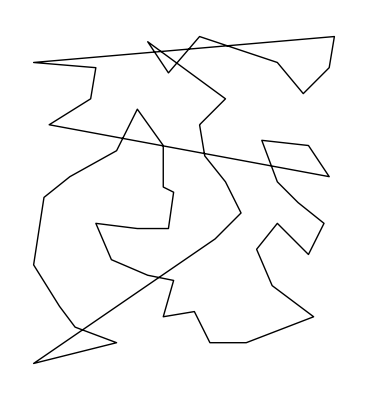

```mathematica
Graphics[Line[pts[[sol]]]]
```

```mathematica
pts[[sol]]
```

Part::partw: Part {1,2,5,3,4,6,505,506,503,504,501,502,507,508,509,510,511,512,513,485,482,481,998,580,579,514,515,523,524,530,999,870,871,872,868,873,867,869,866,865,864,863,862,861,860,859,856,855,854,857,«953»} of {{1150,4000},{1050,2750},{1150,2250},{1250,2050},{1350,2350},{1050,1550},{3350,1700},{3450,1450},{3550,1600},{3950,1700},{4050,2000},{4050,2150},{4250,1650},«25»,{5050,3100},{4950,3300},{5100,3600},{5200,3650},{5350,3750},{5450,3750},{5600,3750},{5600,4250},{5450,4250},{5350,4150},{5050,3800},{4950,3500},«951»} does not exist.

{{1150,4000},{1050,2750},{1150,2250},{1250,2050},{1350,2350},{1050,1550},{3350,1700},{3450,1450},{3550,1600},{3950,1700},{4050,2000},{4050,2150},{4250,1650},{4150,1500},{4450,1450},{4400,1700},{4600,1850},{4900,1550},{5100,1550},{5350,1450},{4950,1700},{4850,1900},{4900,2050},{5000,2150},{5100,2050},{5400,2050},{5750,2000},{5900,2050},{5600,2250},{5400,2300},{5250,2250},{5000,2350},{5000,2550},{5050,2800},{5250,2750},{5450,2750},{5400,2950},{5200,3150},{5050,3100},{4950,3300},{5100,3600},{5200,3650},{5350,3750},{5450,3750},{5600,3750},{5600,4250},{5450,4250},{5350,4150},{5050,3800},{4950,3500},{4700,3500},{4400,3700},{4450,3500},{4100,3500},{4150,3300},{4100,3150},{4300,3300},{4500,3150},{4500,2950},{4700,3000},{4700,2800},{4700,2500},{4600,2350},{4550,2500},{4550,2800},{4300,2800},{4100,2950},{3700,2800},{3550,2800},{3400,2700},{3400,3200},{3700,3100},{3550,3300},{3350,4250},{3350,4650},{3250,5200},{4000,5050},{4100,4750},{3950,4650},{3950,4250},{4200,4150},{4200,4550},{4500,4400},{4700,4350},{4700,4750},{4500,4800},{4500,4950},{4350,4750},{4350,4900},{4247,5150},{4354,5256},{4247,5256},{4100,5250},{4100,5350},{4000,5550},{4199,5554},{4305,5554},{4304,5447},{4500,5450},{4500,6050},{4650,6000},{4800,6100},{5050,6050},{5150,6150},{5300,6050},{5400,6050},{5150,5500},{5250,5350},{5300,5150},{5650,5350},{5800,5350},{5650,5500},{5800,5500},{5750,5700},{5750,5850},{5700,6000},{5700,6150},{5550,6000},{5550,6150},{6000,6600},{6000,7000},{5550,6650},{5400,6550},{5300,6450},{5150,6550},{5150,7000},{5050,6550},{4800,6500},{4650,6400},{4500,6550},{4250,6700},{4250,6350},{4250,5950},{4100,5850},{3950,5950},{3800,5950},{3950,6350},{3800,6350},{3250,7000},{3300,7450},{3300,7550},{3900,7850},{4250,7800},{4400,7750},{4250,7300},{4450,7450},{4650,7450},{4550,7650},{4550,7900},{4650,8150},{4400,8250},{4250,8250},{4550,8750},{4550,8950},{4250,9250},{4300,9450},{4500,9750},{4300,9950},{4300,10150},{4100,10150},{3900,10150},{4200,9850},{4050,9700},{4200,9450},{4050,9200},{3900,9250},{3750,9500},{3450,9450},{3300,9350},{3300,10650},{3450,10450},{3750,10500},{3600,11100},{3750,11200},{3750,11400},{3600,11600},{3900,11550},{3900,11400},{3900,11150},{4100,11150},{4300,11150},{4600,11100},{4600,10850},{4550,10550},{4500,10250},{5600,9750},{5600,10250},{5950,10250},{6100,10250},{6250,10200},{6400,10300},{6200,10300},{6150,10400},{5950,10550},{5650,10550},{5600,10850},{5950,10850},{6050,11050},{6150,11050},{6200,11150},{5950,11150},{5600,11100},{5950,11650},{6050,11550},{6450,11550},{6350,11350},{6550,11350},{6500,11150},{6650,11050},{6950,11250},{6950,10650},{7000,10500},{7200,10500},{7200,10200},{7100,10250},{7050,10400},{6900,10450},{6700,10300},{6850,10200},{7000,10050},{6800,9950},{7000,9800},{7100,9750},{7300,9650},{7300,9350},{7300,9150},{7300,9000},{7000,9000},{6900,9000},{6950,9250},{6700,9150},{6800,9350},{6700,9650},{6700,9800},{6600,9800},{6500,10050},{6400,10050},{6200,9950},{6100,10050},{6100,9800},{5950,9750},{6000,9600},{6150,9200},{6250,8950},{6250,8850},{6350,8850},{6150,8600},{6150,8500},{6000,8450},{6000,8600},{5550,8950},{5550,8750},{5650,8150},{5550,7900},{5550,7650},{5650,7450},{5900,7350},{5950,7650},{6000,7850},{6400,8350},{6450,8600},{6500,8700},{6500,9000},{6600,9000},{6699,8856},{6699,8750},{6805,8749},{6750,8600},{6750,8500},{6600,8000},{6900,8350},{7200,8000},{7350,7650},{7000,7350},{7100,6750},{7100,6600},{6800,6000},{6603,6057},{6498,6057},{6604,5950},{6700,5800},{6600,5700},{6550,5500},{6800,5500},{7100,5500},{7100,5100},{7350,4900},{7350,4750},{7350,4150},{7350,4050},{7350,3900},{7350,3800},{6950,3900},{6850,3800},{6850,4050},{6950,4150},{6650,4900},{6700,5050},{6700,5300},{6600,5200},{6250,5500},{6106,5606},{5999,5607},{5998,5500},{6250,5000},{6100,4800},{6000,4450},{6100,4400},{6100,4150},{6000,3950},{6000,3800},{5850,3750},{5750,3450},{5850,3050},{6000,3200},{6000,3300},{6100,3650},{6148,3556},{6148,3450},{6254,3557},{6450,3750},{6450,3650},{6450,3450},{6254,3206},{6148,3206},{6148,3099},{6450,2950},{6450,2800},{6300,2800},{6150,2800},{6000,2800},{6150,2300},{6300,2300},{6450,2300},{8100,1700},{8200,1450},{8300,1600},{8700,1700},{8800,2000},{8800,2150},{9000,1650},{8900,1500},{9200,1450},{9150,1700},{9350,1850},{9650,1550},{9850,1550},{10100,1450},{9700,1700},{9600,1900},{9650,2050},{9750,2150},{9850,2050},{10150,2050},{10500,2000},{10650,2050},{10350,2250},{10150,2300},{10000,2250},{9750,2350},{9750,2550},{9800,2800},{10000,2750},{10200,2750},{10150,2950},{9950,3150},{9800,3100},{9700,3300},{9850,3600},{9950,3650},{10100,3750},{10200,3750},{10350,3750},{10350,4250},{10200,4250},{10100,4150},{9800,3800},{9700,3500},{9450,3500},{9150,3700},{9200,3500},{8850,3500},{8900,3300},{8850,3150},{9050,3300},{9250,3150},{9250,2950},{9450,3000},{9450,2800},{9450,2500},{9350,2350},{9300,2500},{9300,2800},{9050,2800},{8850,2950},{8450,2800},{8300,2800},{8150,2700},{8150,3200},{8450,3100},{8300,3300},{8100,4250},{8100,4650},{8000,5200},{8750,5050},{8850,4750},{8700,4650},{8700,4250},{8950,4150},{8950,4550},{9250,4400},{9450,4350},{9450,4750},{9250,4800},{9250,4950},{9100,4750},{9100,4900},{8997,5150},{9104,5256},{8997,5256},{8850,5250},{8850,5350},{8750,5550},{8949,5554},{9055,5554},{9054,5447},{9250,5450},{9250,6050},{9400,6000},{9550,6100},{9800,6050},{9900,6150},{10050,6050},{10150,6050},{9900,5500},{10000,5350},{10050,5150},{10400,5350},{10550,5350},{10400,5500},{10550,5500},{10500,5700},{10500,5850},{10450,6000},{10450,6150},{10300,6000},{10300,6150},{10750,6600},{10750,7000},{10300,6650},{10150,6550},{10050,6450},{9900,6550},{9900,7000},{9800,6550},{9550,6500},{9400,6400},{9250,6550},{9000,6700},{9000,6350},{9000,5950},{8850,5850},{8700,5950},{8550,5950},{8700,6350},{8550,6350},{8000,7000},{8050,7450},{8050,7550},{8650,7850},{9000,7800},{9150,7750},{9000,7300},{9200,7450},{9400,7450},{9300,7650},{9300,7900},{9400,8150},{9150,8250},{9000,8250},{9300,8750},{9300,8950},{9000,9250},{9050,9450},{9250,9750},{9050,9950},{9050,10150},{8850,10150},{8650,10150},{8950,9850},{8800,9700},{8950,9450},{8800,9200},{8650,9250},{8500,9500},{8200,9450},{8050,9350},{8050,10650},{8200,10450},{8500,10500},{8350,11100},{8500,11200},{8500,11400},{8350,11600},{8650,11550},{8650,11400},{8650,11150},{8850,11150},{9050,11150},{9350,11100},{9350,10850},{9300,10550},{9250,10250},{10350,9750},{10350,10250},{10700,10250},{10850,10250},{11000,10200},{11150,10300},{10950,10300},{10900,10400},{10700,10550},{10400,10550},{10350,10850},{10700,10850},{10800,11050},{10900,11050},{10950,11150},{10700,11150},{10350,11100},{10700,11650},{10800,11550},{11200,11550},{11100,11350},{11300,11350},{11250,11150},{11400,11050},{11700,11250},{11700,10650},{11750,10500},{11950,10500},{11950,10200},{11850,10250},{11800,10400},{11650,10450},{11450,10300},{11600,10200},{11750,10050},{11550,9950},{11750,9800},{11850,9750},{12050,9650},{12050,9350},{12050,9150},{12050,9000},{11750,9000},{11650,9000},{11700,9250},{11450,9150},{11550,9350},{11450,9650},{11450,9800},{11350,9800},{11250,10050},{11150,10050},{10950,9950},{10850,10050},{10850,9800},{10700,9750},{10750,9600},{10900,9200},{11000,8950},{11000,8850},{11100,8850},{10900,8600},{10900,8500},{10750,8450},{10750,8600},{10300,8950},{10300,8750},{10400,8150},{10300,7900},{10300,7650},{10400,7450},{10650,7350},{10700,7650},{10750,7850},{11150,8350},{11200,8600},{11250,8700},{11250,9000},{11350,9000},{11449,8856},{11449,8750},{11555,8749},{11500,8600},{11500,8500},{11350,8000},{11650,8350},{11950,8000},{12100,7650},{11750,7350},{11850,6750},{11850,6600},{11550,6000},{11353,6057},{11248,6057},{11354,5950},{11450,5800},{11350,5700},{11300,5500},{11550,5500},{11850,5500},{11850,5100},{12100,4900},{12100,4750},{12100,4150},{12100,4050},{12100,3900},{12100,3800},{11700,3900},{11600,3800},{11600,4050},{11700,4150},{11400,4900},{11450,5050},{11450,5300},{11350,5200},{11000,5500},{10856,5606},{10749,5607},{10748,5500},{11000,5000},{10850,4800},{10750,4450},{10850,4400},{10850,4150},{10750,3950},{10750,3800},{10600,3750},{10500,3450},{10600,3050},{10750,3200},{10750,3300},{10850,3650},{10898,3556},{10898,3450},{11004,3557},{11200,3750},{11200,3650},{11200,3450},{11004,3206},{10898,3206},{10898,3099},{11200,2950},{11200,2800},{11050,2800},{10900,2800},{10750,2800},{10900,2300},{11050,2300},{11200,2300},{12850,1700},{12950,1450},{13050,1600},{13450,1700},{13550,2000},{13550,2150},{13750,1650},{13650,1500},{13950,1450},{13900,1700},{14100,1850},{14400,1550},{14600,1550},{14850,1450},{14450,1700},{14350,1900},{14400,2050},{14500,2150},{14600,2050},{14900,2050},{15250,2000},{15400,2050},{15100,2250},{14900,2300},{14750,2250},{14500,2350},{14500,2550},{14550,2800},{14750,2750},{14950,2750},{14900,2950},{14700,3150},{14550,3100},{14450,3300},{14600,3600},{14700,3650},{14850,3750},{14950,3750},{15100,3750},{15100,4250},{14950,4250},{14850,4150},{14550,3800},{14450,3500},{14200,3500},{13900,3700},{13950,3500},{13600,3500},{13650,3300},{13600,3150},{13800,3300},{14000,3150},{14000,2950},{14200,3000},{14200,2800},{14200,2500},{14100,2350},{14050,2500},{14050,2800},{13800,2800},{13600,2950},{13200,2800},{13050,2800},{12900,2700},{12900,3200},{13200,3100},{13050,3300},{12850,4250},{12850,4650},{12750,5200},{13500,5050},{13600,4750},{13450,4650},{13450,4250},{13700,4150},{13700,4550},{14000,4400},{14200,4350},{14200,4750},{14000,4800},{14000,4950},{13850,4750},{13850,4900},{13747,5150},{13854,5256},{13747,5256},{13600,5250},{13600,5350},{13500,5550},{13699,5554},{13805,5554},{13804,5447},{14000,5450},{14000,6050},{14150,6000},{14300,6100},{14550,6050},{14650,6150},{14800,6050},{14900,6050},{14650,5500},{14750,5350},{14800,5150},{15150,5350},{15300,5350},{15150,5500},{15300,5500},{15250,5700},{15250,5850},{15200,6000},{15200,6150},{15050,6000},{15050,6150},{15500,6600},{15500,7000},{15050,6650},{14900,6550},{14800,6450},{14650,6550},{14650,7000},{14550,6550},{14300,6500},{14150,6400},{14000,6550},{13750,6700},{13750,6350},{13750,5950},{13600,5850},{13450,5950},{13300,5950},{13450,6350},{13300,6350},{12750,7000},{12800,7450},{12800,7550},{13400,7850},{13750,7800},{13900,7750},{13750,7300},{13950,7450},{14150,7450},{14050,7650},{14050,7900},{14150,8150},{13900,8250},{13750,8250},{14050,8750},{14050,8950},{13750,9250},{13800,9450},{14000,9750},{13800,9950},{13800,10150},{13600,10150},{13400,10150},{13700,9850},{13550,9700},{13700,9450},{13550,9200},{13400,9250},{13250,9500},{12950,9450},{12800,9350},{12800,10650},{12950,10450},{13250,10500},{13100,11100},{13250,11200},{13250,11400},{13100,11600},{13400,11550},{13400,11400},{13400,11150},{13600,11150},{13800,11150},{14100,11100},{14100,10850},{14050,10550},{14000,10250},{15100,9750},{15100,10250},{15450,10250},{15600,10250},{15750,10200},{15900,10300},{15700,10300},{15650,10400},{15450,10550},{15150,10550},{15100,10850},{15450,10850},{15550,11050},{15650,11050},{15700,11150},{15450,11150},{15100,11100},{15450,11650},{15550,11550},{15950,11550},{15850,11350},{16050,11350},{16000,11150},{16150,11050},{16450,11250},{16450,10650},{16500,10500},{16700,10500},{16700,10200},{16600,10250},{16550,10400},{16400,10450},{16200,10300},{16350,10200},{16500,10050},{16300,9950},{16500,9800},{16600,9750},{16800,9650},{16800,9350},{16800,9150},{16800,9000},{16500,9000},{16400,9000},{16450,9250},{16200,9150},{16300,9350},{16200,9650},{16200,9800},{16100,9800},{16000,10050},{15900,10050},{15700,9950},{15600,10050},{15600,9800},{15450,9750},{15500,9600},{15650,9200},{15750,8950},{15750,8850},{15850,8850},{15650,8600},{15650,8500},{15500,8450},{15500,8600},{15050,8950},{15050,8750},{15150,8150},{15050,7900},{15050,7650},{15150,7450},{15400,7350},{15450,7650},{15500,7850},{15900,8350},{15950,8600},{16000,8700},{16000,9000},{16100,9000},{16199,8856},{16199,8750},{16305,8749},{16250,8600},{16250,8500},{16100,8000},{16400,8350},{16700,8000},{16850,7650},{16500,7350},{16600,6750},{16600,6600},{16300,6000},{16103,6057},{15998,6057},{16104,5950},{16200,5800},{16100,5700},{16050,5500},{16300,5500},{16600,5500},{16600,5100},{16850,4900},{16850,4750},{16850,4150},{16850,4050},{16850,3900},{16850,3800},{16450,3900},{16350,3800},{16350,4050},{16450,4150},{16150,4900},{16200,5050},{16200,5300},{16100,5200},{15750,5500},{15606,5606},{15499,5607},{15498,5500},{15750,5000},{15600,4800},{15500,4450},{15600,4400},{15600,4150},{15500,3950},{15500,3800},{15350,3750},{15250,3450},{15350,3050},{15500,3200},{15500,3300},{15600,3650},{15648,3556},{15648,3450},{15754,3557},{15950,3750},{15950,3650},{15950,3450},{15754,3206},{15648,3206},{15648,3099},{15950,2950},{15950,2800},{15800,2800},{15650,2800},{15500,2800},{15650,2300},{15800,2300},{15950,2300},{6450,4950},{11200,4950},{15950,4950},{5050,5750},{5050,8450},{5050,11650},{9800,5750},{9800,8450},{9800,11650},{14550,5750},{14550,8450}}⟦{1,2,5,3,4,6,505,506,503,504,501,502,507,508,509,510,511,512,513,485,482,481,998,580,579,514,515,523,524,530,999,870,871,872,868,873,867,869,866,865,864,863,862,861,860,859,856,855,854,857,853,850,849,1002,858,852,851,843,842,898,897,896,894,895,844,845,848,846,847,893,892,874,875,876,877,891,890,889,878,879,880,881,882,883,884,885,887,888,886,899,907,908,1001,809,810,813,841,840,839,838,837,836,835,830,829,832,831,834,833,826,827,828,817,816,815,814,818,819,820,812,811,821,822,823,824,825,598,587,586,585,584,583,582,581,577,578,575,576,588,589,590,574,573,572,571,570,569,568,566,567,516,517,520,521,522,525,529,526,527,528,531,532,533,534,535,536,537,538,541,539,545,540,544,543,542,561,562,563,564,565,518,519,546,547,548,549,550,551,552,553,554,555,556,557,558,560,559,591,592,593,594,595,596,597,599,600,601,602,603,604,795,796,797,798,808,807,806,805,799,800,804,803,802,801,782,777,776,778,779,780,781,783,784,785,786,787,788,793,794,792,791,790,789,756,757,758,759,760,761,762,774,772,773,775,771,770,766,768,769,767,960,959,958,957,932,931,930,929,928,927,925,924,923,922,921,920,919,900,901,902,918,917,916,904,903,906,905,909,910,911,912,913,914,915,926,990,989,988,684,683,685,686,687,682,681,680,679,678,677,674,675,676,671,673,672,669,670,666,667,668,719,720,718,688,689,690,691,692,693,694,695,696,706,697,698,699,700,701,968,967,966,965,964,963,962,961,993,953,954,956,955,940,939,938,937,936,934,935,933,941,942,943,944,948,947,946,945,952,951,949,950,977,978,979,976,975,974,973,969,972,971,982,981,980,983,984,985,986,987,970,716,717,721,715,714,722,723,712,711,713,709,708,707,705,704,703,702,765,764,763,1000,755,754,753,752,751,750,749,746,748,747,745,744,742,743,741,740,739,738,734,735,736,737,710,727,729,728,724,725,726,663,665,664,733,732,731,730,620,619,618,617,624,623,621,622,649,650,651,648,647,646,645,641,644,643,654,653,652,655,656,657,658,659,642,662,661,660,356,355,354,357,358,359,353,352,351,350,349,346,347,348,343,345,344,341,342,338,339,340,335,337,336,398,397,396,400,401,399,388,389,393,387,386,385,383,384,395,394,391,392,390,360,361,362,363,364,365,366,367,368,378,369,370,371,372,373,640,639,638,637,636,635,634,633,992,625,626,628,627,612,611,610,609,608,606,607,605,613,614,615,616,374,375,376,377,379,381,380,382,409,408,407,406,410,411,412,413,415,414,416,417,419,420,418,421,422,423,424,425,426,427,997,435,436,437,629,630,631,632,438,439,441,440,442,443,444,445,447,446,434,433,432,431,430,429,428,461,462,463,464,466,465,460,459,458,457,456,455,453,452,451,450,448,449,454,473,475,474,476,472,471,477,478,479,480,470,469,468,467,276,275,274,273,272,271,269,268,267,266,265,264,263,246,245,244,243,242,241,240,238,239,188,189,193,192,190,191,237,236,218,219,220,221,235,234,233,222,223,224,225,226,227,228,229,231,232,230,262,261,260,248,247,250,249,253,254,255,256,257,258,259,270,497,496,495,494,493,483,492,484,491,490,486,487,488,489,500,499,498,214,215,216,212,217,211,213,210,209,208,207,206,205,204,203,200,199,198,201,197,194,195,196,202,996,187,186,251,252,995,153,154,157,185,184,183,182,181,180,179,174,173,176,175,178,177,170,171,172,161,160,159,158,162,163,164,156,155,165,166,167,168,169,139,140,141,142,152,151,150,149,143,144,148,146,147,145,126,121,120,122,123,124,125,127,128,129,130,131,132,137,138,136,135,134,133,100,101,102,103,104,105,106,118,116,117,119,115,114,112,110,111,113,304,303,302,301,109,108,107,994,99,98,97,96,95,94,93,90,92,91,89,88,86,87,85,84,83,82,78,79,80,81,54,52,53,51,49,48,47,46,60,61,65,59,58,57,55,56,67,66,63,64,62,32,33,34,35,36,37,38,39,40,50,41,42,43,44,45,312,311,310,309,308,307,306,305,991,297,298,300,299,284,283,282,281,280,278,279,277,285,286,287,288,405,404,403,402,292,291,290,289,296,295,293,294,321,322,323,320,319,318,317,313,324,325,326,315,316,314,331,330,329,328,327,334,333,332,28,27,26,29,30,31,25,24,23,22,21,18,19,20,15,17,16,13,14,10,11,12,7,9,8,70,69,68,72,73,71,74,75,76,77,1}⟧

```mathematica
SolIn["/home/pi/Downloads/concorde/KDTREE/pr1002_greedy.sol"][[1]]
```

Part::partw: Part {1,2,5,3,4,6,505,506,503,504,501,502,507,508,509,510,511,512,513,485,482,481,998,580,579,514,515,523,524,530,999,870,871,872,868,873,867,869,866,865,864,863,862,861,860,859,856,855,854,857,«953»} of {{1150,4000},{1050,2750},{1150,2250},{1250,2050},{1350,2350},{1050,1550},{3350,1700},{3450,1450},{3550,1600},{3950,1700},{4050,2000},{4050,2150},{4250,1650},«25»,{5050,3100},{4950,3300},{5100,3600},{5200,3650},{5350,3750},{5450,3750},{5600,3750},{5600,4250},{5450,4250},{5350,4150},{5050,3800},{4950,3500},«951»} does not exist.

ArcLength::reg: Line[{{1150,4000},{1050,2750},{1150,2250},{1250,2050},{1350,2350},{1050,1550},{3350,1700},{3450,1450},{3550,1600},{3950,1700},{4050,2000},{4050,2150},{4250,1650},«26»,{4950,3300},{5100,3600},{5200,3650},{5350,3750},{5450,3750},{5600,3750},{5600,4250},{5450,4250},{5350,4150},{5050,3800},{4950,3500},«951»}⟦{«1»}⟧] is not a correctly specified region.

Part::partw: Part {1,2,5,3,4,6,505,506,503,504,501,502,507,508,509,510,511,512,513,485,482,481,998,580,579,514,515,523,524,530,999,870,871,872,868,873,867,869,866,865,864,863,862,861,860,859,856,855,854,857,«953»} of {{1150.,4000.},{1050.,2750.},{1150.,2250.},{1250.,2050.},{1350.,2350.},{1050.,1550.},{3350.,1700.},{3450.,1450.},{3550.,1600.},{3950.,1700.},«31»,{5200.,3650.},{5350.,3750.},{5450.,3750.},{5600.,3750.},{5600.,4250.},{5450.,4250.},{5350.,4150.},{5050.,3800.},{4950.,3500.},«951»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ArcLength::reg: Line[{{1150.,4000.},{1050.,2750.},{1150.,2250.},{1250.,2050.},{1350.,2350.},{1050.,1550.},{3350.,1700.},{3450.,1450.},{3550.,1600.},«33»,{5350.,3750.},{5450.,3750.},{5600.,3750.},{5600.,4250.},{5450.,4250.},{5350.,4150.},{5050.,3800.},{4950.,3500.},«951»}⟦{1,2,5,«46»,857,«953»}⟧] is not a correctly specified region.

ArcLength[Line[{{1150.,4000.},{1050.,2750.},{1150.,2250.},{1250.,2050.},{1350.,2350.},{1050.,1550.},{3350.,1700.},{3450.,1450.},{3550.,1600.},{3950.,1700.},{4050.,2000.},{4050.,2150.},{4250.,1650.},{4150.,1500.},{4450.,1450.},{4400.,1700.},{4600.,1850.},{4900.,1550.},{5100.,1550.},{5350.,1450.},{4950.,1700.},{4850.,1900.},{4900.,2050.},{5000.,2150.},{5100.,2050.},{5400.,2050.},{5750.,2000.},{5900.,2050.},{5600.,2250.},{5400.,2300.},{5250.,2250.},{5000.,2350.},{5000.,2550.},{5050.,2800.},{5250.,2750.},{5450.,2750.},{5400.,2950.},{5200.,3150.},{5050.,3100.},{4950.,3300.},{5100.,3600.},{5200.,3650.},{5350.,3750.},{5450.,3750.},{5600.,3750.},{5600.,4250.},{5450.,4250.},{5350.,4150.},{5050.,3800.},{4950.,3500.},{4700.,3500.},{4400.,3700.},{4450.,3500.},{4100.,3500.},{4150.,3300.},{4100.,3150.},{4300.,3300.},{4500.,3150.},{4500.,2950.},{4700.,3000.},{4700.,2800.},{4700.,2500.},{4600.,2350.},{4550.,2500.},{4550.,2800.},{4300.,2800.},{4100.,2950.},{3700.,2800.},{3550.,2800.},{3400.,2700.},{3400.,3200.},{3700.,3100.},{3550.,3300.},{3350.,4250.},{3350.,4650.},{3250.,5200.},{4000.,5050.},{4100.,4750.},{3950.,4650.},{3950.,4250.},{4200.,4150.},{4200.,4550.},{4500.,4400.},{4700.,4350.},{4700.,4750.},{4500.,4800.},{4500.,4950.},{4350.,4750.},{4350.,4900.},{4247.,5150.},{4354.,5256.},{4247.,5256.},{4100.,5250.},{4100.,5350.},{4000.,5550.},{4199.,5554.},{4305.,5554.},{4304.,5447.},{4500.,5450.},{4500.,6050.},{4650.,6000.},{4800.,6100.},{5050.,6050.},{5150.,6150.},{5300.,6050.},{5400.,6050.},{5150.,5500.},{5250.,5350.},{5300.,5150.},{5650.,5350.},{5800.,5350.},{5650.,5500.},{5800.,5500.},{5750.,5700.},{5750.,5850.},{5700.,6000.},{5700.,6150.},{5550.,6000.},{5550.,6150.},{6000.,6600.},{6000.,7000.},{5550.,6650.},{5400.,6550.},{5300.,6450.},{5150.,6550.},{5150.,7000.},{5050.,6550.},{4800.,6500.},{4650.,6400.},{4500.,6550.},{4250.,6700.},{4250.,6350.},{4250.,5950.},{4100.,5850.},{3950.,5950.},{3800.,5950.},{3950.,6350.},{3800.,6350.},{3250.,7000.},{3300.,7450.},{3300.,7550.},{3900.,7850.},{4250.,7800.},{4400.,7750.},{4250.,7300.},{4450.,7450.},{4650.,7450.},{4550.,7650.},{4550.,7900.},{4650.,8150.},{4400.,8250.},{4250.,8250.},{4550.,8750.},{4550.,8950.},{4250.,9250.},{4300.,9450.},{4500.,9750.},{4300.,9950.},{4300.,10150.},{4100.,10150.},{3900.,10150.},{4200.,9850.},{4050.,9700.},{4200.,9450.},{4050.,9200.},{3900.,9250.},{3750.,9500.},{3450.,9450.},{3300.,9350.},{3300.,10650.},{3450.,10450.},{3750.,10500.},{3600.,11100.},{3750.,11200.},{3750.,11400.},{3600.,11600.},{3900.,11550.},{3900.,11400.},{3900.,11150.},{4100.,11150.},{4300.,11150.},{4600.,11100.},{4600.,10850.},{4550.,10550.},{4500.,10250.},{5600.,9750.},{5600.,10250.},{5950.,10250.},{6100.,10250.},{6250.,10200.},{6400.,10300.},{6200.,10300.},{6150.,10400.},{5950.,10550.},{5650.,10550.},{5600.,10850.},{5950.,10850.},{6050.,11050.},{6150.,11050.},{6200.,11150.},{5950.,11150.},{5600.,11100.},{5950.,11650.},{6050.,11550.},{6450.,11550.},{6350.,11350.},{6550.,11350.},{6500.,11150.},{6650.,11050.},{6950.,11250.},{6950.,10650.},{7000.,10500.},{7200.,10500.},{7200.,10200.},{7100.,10250.},{7050.,10400.},{6900.,10450.},{6700.,10300.},{6850.,10200.},{7000.,10050.},{6800.,9950.},{7000.,9800.},{7100.,9750.},{7300.,9650.},{7300.,9350.},{7300.,9150.},{7300.,9000.},{7000.,9000.},{6900.,9000.},{6950.,9250.},{6700.,9150.},{6800.,9350.},{6700.,9650.},{6700.,9800.},{6600.,9800.},{6500.,10050.},{6400.,10050.},{6200.,9950.},{6100.,10050.},{6100.,9800.},{5950.,9750.},{6000.,9600.},{6150.,9200.},{6250.,8950.},{6250.,8850.},{6350.,8850.},{6150.,8600.},{6150.,8500.},{6000.,8450.},{6000.,8600.},{5550.,8950.},{5550.,8750.},{5650.,8150.},{5550.,7900.},{5550.,7650.},{5650.,7450.},{5900.,7350.},{5950.,7650.},{6000.,7850.},{6400.,8350.},{6450.,8600.},{6500.,8700.},{6500.,9000.},{6600.,9000.},{6699.,8856.},{6699.,8750.},{6805.,8749.},{6750.,8600.},{6750.,8500.},{6600.,8000.},{6900.,8350.},{7200.,8000.},{7350.,7650.},{7000.,7350.},{7100.,6750.},{7100.,6600.},{6800.,6000.},{6603.,6057.},{6498.,6057.},{6604.,5950.},{6700.,5800.},{6600.,5700.},{6550.,5500.},{6800.,5500.},{7100.,5500.},{7100.,5100.},{7350.,4900.},{7350.,4750.},{7350.,4150.},{7350.,4050.},{7350.,3900.},{7350.,3800.},{6950.,3900.},{6850.,3800.},{6850.,4050.},{6950.,4150.},{6650.,4900.},{6700.,5050.},{6700.,5300.},{6600.,5200.},{6250.,5500.},{6106.,5606.},{5999.,5607.},{5998.,5500.},{6250.,5000.},{6100.,4800.},{6000.,4450.},{6100.,4400.},{6100.,4150.},{6000.,3950.},{6000.,3800.},{5850.,3750.},{5750.,3450.},{5850.,3050.},{6000.,3200.},{6000.,3300.},{6100.,3650.},{6148.,3556.},{6148.,3450.},{6254.,3557.},{6450.,3750.},{6450.,3650.},{6450.,3450.},{6254.,3206.},{6148.,3206.},{6148.,3099.},{6450.,2950.},{6450.,2800.},{6300.,2800.},{6150.,2800.},{6000.,2800.},{6150.,2300.},{6300.,2300.},{6450.,2300.},{8100.,1700.},{8200.,1450.},{8300.,1600.},{8700.,1700.},{8800.,2000.},{8800.,2150.},{9000.,1650.},{8900.,1500.},{9200.,1450.},{9150.,1700.},{9350.,1850.},{9650.,1550.},{9850.,1550.},{10100.,1450.},{9700.,1700.},{9600.,1900.},{9650.,2050.},{9750.,2150.},{9850.,2050.},{10150.,2050.},{10500.,2000.},{10650.,2050.},{10350.,2250.},{10150.,2300.},{10000.,2250.},{9750.,2350.},{9750.,2550.},{9800.,2800.},{10000.,2750.},{10200.,2750.},{10150.,2950.},{9950.,3150.},{9800.,3100.},{9700.,3300.},{9850.,3600.},{9950.,3650.},{10100.,3750.},{10200.,3750.},{10350.,3750.},{10350.,4250.},{10200.,4250.},{10100.,4150.},{9800.,3800.},{9700.,3500.},{9450.,3500.},{9150.,3700.},{9200.,3500.},{8850.,3500.},{8900.,3300.},{8850.,3150.},{9050.,3300.},{9250.,3150.},{9250.,2950.},{9450.,3000.},{9450.,2800.},{9450.,2500.},{9350.,2350.},{9300.,2500.},{9300.,2800.},{9050.,2800.},{8850.,2950.},{8450.,2800.},{8300.,2800.},{8150.,2700.},{8150.,3200.},{8450.,3100.},{8300.,3300.},{8100.,4250.},{8100.,4650.},{8000.,5200.},{8750.,5050.},{8850.,4750.},{8700.,4650.},{8700.,4250.},{8950.,4150.},{8950.,4550.},{9250.,4400.},{9450.,4350.},{9450.,4750.},{9250.,4800.},{9250.,4950.},{9100.,4750.},{9100.,4900.},{8997.,5150.},{9104.,5256.},{8997.,5256.},{8850.,5250.},{8850.,5350.},{8750.,5550.},{8949.,5554.},{9055.,5554.},{9054.,5447.},{9250.,5450.},{9250.,6050.},{9400.,6000.},{9550.,6100.},{9800.,6050.},{9900.,6150.},{10050.,6050.},{10150.,6050.},{9900.,5500.},{10000.,5350.},{10050.,5150.},{10400.,5350.},{10550.,5350.},{10400.,5500.},{10550.,5500.},{10500.,5700.},{10500.,5850.},{10450.,6000.},{10450.,6150.},{10300.,6000.},{10300.,6150.},{10750.,6600.},{10750.,7000.},{10300.,6650.},{10150.,6550.},{10050.,6450.},{9900.,6550.},{9900.,7000.},{9800.,6550.},{9550.,6500.},{9400.,6400.},{9250.,6550.},{9000.,6700.},{9000.,6350.},{9000.,5950.},{8850.,5850.},{8700.,5950.},{8550.,5950.},{8700.,6350.},{8550.,6350.},{8000.,7000.},{8050.,7450.},{8050.,7550.},{8650.,7850.},{9000.,7800.},{9150.,7750.},{9000.,7300.},{9200.,7450.},{9400.,7450.},{9300.,7650.},{9300.,7900.},{9400.,8150.},{9150.,8250.},{9000.,8250.},{9300.,8750.},{9300.,8950.},{9000.,9250.},{9050.,9450.},{9250.,9750.},{9050.,9950.},{9050.,10150.},{8850.,10150.},{8650.,10150.},{8950.,9850.},{8800.,9700.},{8950.,9450.},{8800.,9200.},{8650.,9250.},{8500.,9500.},{8200.,9450.},{8050.,9350.},{8050.,10650.},{8200.,10450.},{8500.,10500.},{8350.,11100.},{8500.,11200.},{8500.,11400.},{8350.,11600.},{8650.,11550.},{8650.,11400.},{8650.,11150.},{8850.,11150.},{9050.,11150.},{9350.,11100.},{9350.,10850.},{9300.,10550.},{9250.,10250.},{10350.,9750.},{10350.,10250.},{10700.,10250.},{10850.,10250.},{11000.,10200.},{11150.,10300.},{10950.,10300.},{10900.,10400.},{10700.,10550.},{10400.,10550.},{10350.,10850.},{10700.,10850.},{10800.,11050.},{10900.,11050.},{10950.,11150.},{10700.,11150.},{10350.,11100.},{10700.,11650.},{10800.,11550.},{11200.,11550.},{11100.,11350.},{11300.,11350.},{11250.,11150.},{11400.,11050.},{11700.,11250.},{11700.,10650.},{11750.,10500.},{11950.,10500.},{11950.,10200.},{11850.,10250.},{11800.,10400.},{11650.,10450.},{11450.,10300.},{11600.,10200.},{11750.,10050.},{11550.,9950.},{11750.,9800.},{11850.,9750.},{12050.,9650.},{12050.,9350.},{12050.,9150.},{12050.,9000.},{11750.,9000.},{11650.,9000.},{11700.,9250.},{11450.,9150.},{11550.,9350.},{11450.,9650.},{11450.,9800.},{11350.,9800.},{11250.,10050.},{11150.,10050.},{10950.,9950.},{10850.,10050.},{10850.,9800.},{10700.,9750.},{10750.,9600.},{10900.,9200.},{11000.,8950.},{11000.,8850.},{11100.,8850.},{10900.,8600.},{10900.,8500.},{10750.,8450.},{10750.,8600.},{10300.,8950.},{10300.,8750.},{10400.,8150.},{10300.,7900.},{10300.,7650.},{10400.,7450.},{10650.,7350.},{10700.,7650.},{10750.,7850.},{11150.,8350.},{11200.,8600.},{11250.,8700.},{11250.,9000.},{11350.,9000.},{11449.,8856.},{11449.,8750.},{11555.,8749.},{11500.,8600.},{11500.,8500.},{11350.,8000.},{11650.,8350.},{11950.,8000.},{12100.,7650.},{11750.,7350.},{11850.,6750.},{11850.,6600.},{11550.,6000.},{11353.,6057.},{11248.,6057.},{11354.,5950.},{11450.,5800.},{11350.,5700.},{11300.,5500.},{11550.,5500.},{11850.,5500.},{11850.,5100.},{12100.,4900.},{12100.,4750.},{12100.,4150.},{12100.,4050.},{12100.,3900.},{12100.,3800.},{11700.,3900.},{11600.,3800.},{11600.,4050.},{11700.,4150.},{11400.,4900.},{11450.,5050.},{11450.,5300.},{11350.,5200.},{11000.,5500.},{10856.,5606.},{10749.,5607.},{10748.,5500.},{11000.,5000.},{10850.,4800.},{10750.,4450.},{10850.,4400.},{10850.,4150.},{10750.,3950.},{10750.,3800.},{10600.,3750.},{10500.,3450.},{10600.,3050.},{10750.,3200.},{10750.,3300.},{10850.,3650.},{10898.,3556.},{10898.,3450.},{11004.,3557.},{11200.,3750.},{11200.,3650.},{11200.,3450.},{11004.,3206.},{10898.,3206.},{10898.,3099.},{11200.,2950.},{11200.,2800.},{11050.,2800.},{10900.,2800.},{10750.,2800.},{10900.,2300.},{11050.,2300.},{11200.,2300.},{12850.,1700.},{12950.,1450.},{13050.,1600.},{13450.,1700.},{13550.,2000.},{13550.,2150.},{13750.,1650.},{13650.,1500.},{13950.,1450.},{13900.,1700.},{14100.,1850.},{14400.,1550.},{14600.,1550.},{14850.,1450.},{14450.,1700.},{14350.,1900.},{14400.,2050.},{14500.,2150.},{14600.,2050.},{14900.,2050.},{15250.,2000.},{15400.,2050.},{15100.,2250.},{14900.,2300.},{14750.,2250.},{14500.,2350.},{14500.,2550.},{14550.,2800.},{14750.,2750.},{14950.,2750.},{14900.,2950.},{14700.,3150.},{14550.,3100.},{14450.,3300.},{14600.,3600.},{14700.,3650.},{14850.,3750.},{14950.,3750.},{15100.,3750.},{15100.,4250.},{14950.,4250.},{14850.,4150.},{14550.,3800.},{14450.,3500.},{14200.,3500.},{13900.,3700.},{13950.,3500.},{13600.,3500.},{13650.,3300.},{13600.,3150.},{13800.,3300.},{14000.,3150.},{14000.,2950.},{14200.,3000.},{14200.,2800.},{14200.,2500.},{14100.,2350.},{14050.,2500.},{14050.,2800.},{13800.,2800.},{13600.,2950.},{13200.,2800.},{13050.,2800.},{12900.,2700.},{12900.,3200.},{13200.,3100.},{13050.,3300.},{12850.,4250.},{12850.,4650.},{12750.,5200.},{13500.,5050.},{13600.,4750.},{13450.,4650.},{13450.,4250.},{13700.,4150.},{13700.,4550.},{14000.,4400.},{14200.,4350.},{14200.,4750.},{14000.,4800.},{14000.,4950.},{13850.,4750.},{13850.,4900.},{13747.,5150.},{13854.,5256.},{13747.,5256.},{13600.,5250.},{13600.,5350.},{13500.,5550.},{13699.,5554.},{13805.,5554.},{13804.,5447.},{14000.,5450.},{14000.,6050.},{14150.,6000.},{14300.,6100.},{14550.,6050.},{14650.,6150.},{14800.,6050.},{14900.,6050.},{14650.,5500.},{14750.,5350.},{14800.,5150.},{15150.,5350.},{15300.,5350.},{15150.,5500.},{15300.,5500.},{15250.,5700.},{15250.,5850.},{15200.,6000.},{15200.,6150.},{15050.,6000.},{15050.,6150.},{15500.,6600.},{15500.,7000.},{15050.,6650.},{14900.,6550.},{14800.,6450.},{14650.,6550.},{14650.,7000.},{14550.,6550.},{14300.,6500.},{14150.,6400.},{14000.,6550.},{13750.,6700.},{13750.,6350.},{13750.,5950.},{13600.,5850.},{13450.,5950.},{13300.,5950.},{13450.,6350.},{13300.,6350.},{12750.,7000.},{12800.,7450.},{12800.,7550.},{13400.,7850.},{13750.,7800.},{13900.,7750.},{13750.,7300.},{13950.,7450.},{14150.,7450.},{14050.,7650.},{14050.,7900.},{14150.,8150.},{13900.,8250.},{13750.,8250.},{14050.,8750.},{14050.,8950.},{13750.,9250.},{13800.,9450.},{14000.,9750.},{13800.,9950.},{13800.,10150.},{13600.,10150.},{13400.,10150.},{13700.,9850.},{13550.,9700.},{13700.,9450.},{13550.,9200.},{13400.,9250.},{13250.,9500.},{12950.,9450.},{12800.,9350.},{12800.,10650.},{12950.,10450.},{13250.,10500.},{13100.,11100.},{13250.,11200.},{13250.,11400.},{13100.,11600.},{13400.,11550.},{13400.,11400.},{13400.,11150.},{13600.,11150.},{13800.,11150.},{14100.,11100.},{14100.,10850.},{14050.,10550.},{14000.,10250.},{15100.,9750.},{15100.,10250.},{15450.,10250.},{15600.,10250.},{15750.,10200.},{15900.,10300.},{15700.,10300.},{15650.,10400.},{15450.,10550.},{15150.,10550.},{15100.,10850.},{15450.,10850.},{15550.,11050.},{15650.,11050.},{15700.,11150.},{15450.,11150.},{15100.,11100.},{15450.,11650.},{15550.,11550.},{15950.,11550.},{15850.,11350.},{16050.,11350.},{16000.,11150.},{16150.,11050.},{16450.,11250.},{16450.,10650.},{16500.,10500.},{16700.,10500.},{16700.,10200.},{16600.,10250.},{16550.,10400.},{16400.,10450.},{16200.,10300.},{16350.,10200.},{16500.,10050.},{16300.,9950.},{16500.,9800.},{16600.,9750.},{16800.,9650.},{16800.,9350.},{16800.,9150.},{16800.,9000.},{16500.,9000.},{16400.,9000.},{16450.,9250.},{16200.,9150.},{16300.,9350.},{16200.,9650.},{16200.,9800.},{16100.,9800.},{16000.,10050.},{15900.,10050.},{15700.,9950.},{15600.,10050.},{15600.,9800.},{15450.,9750.},{15500.,9600.},{15650.,9200.},{15750.,8950.},{15750.,8850.},{15850.,8850.},{15650.,8600.},{15650.,8500.},{15500.,8450.},{15500.,8600.},{15050.,8950.},{15050.,8750.},{15150.,8150.},{15050.,7900.},{15050.,7650.},{15150.,7450.},{15400.,7350.},{15450.,7650.},{15500.,7850.},{15900.,8350.},{15950.,8600.},{16000.,8700.},{16000.,9000.},{16100.,9000.},{16199.,8856.},{16199.,8750.},{16305.,8749.},{16250.,8600.},{16250.,8500.},{16100.,8000.},{16400.,8350.},{16700.,8000.},{16850.,7650.},{16500.,7350.},{16600.,6750.},{16600.,6600.},{16300.,6000.},{16103.,6057.},{15998.,6057.},{16104.,5950.},{16200.,5800.},{16100.,5700.},{16050.,5500.},{16300.,5500.},{16600.,5500.},{16600.,5100.},{16850.,4900.},{16850.,4750.},{16850.,4150.},{16850.,4050.},{16850.,3900.},{16850.,3800.},{16450.,3900.},{16350.,3800.},{16350.,4050.},{16450.,4150.},{16150.,4900.},{16200.,5050.},{16200.,5300.},{16100.,5200.},{15750.,5500.},{15606.,5606.},{15499.,5607.},{15498.,5500.},{15750.,5000.},{15600.,4800.},{15500.,4450.},{15600.,4400.},{15600.,4150.},{15500.,3950.},{15500.,3800.},{15350.,3750.},{15250.,3450.},{15350.,3050.},{15500.,3200.},{15500.,3300.},{15600.,3650.},{15648.,3556.},{15648.,3450.},{15754.,3557.},{15950.,3750.},{15950.,3650.},{15950.,3450.},{15754.,3206.},{15648.,3206.},{15648.,3099.},{15950.,2950.},{15950.,2800.},{15800.,2800.},{15650.,2800.},{15500.,2800.},{15650.,2300.},{15800.,2300.},{15950.,2300.},{6450.,4950.},{11200.,4950.},{15950.,4950.},{5050.,5750.},{5050.,8450.},{5050.,11650.},{9800.,5750.},{9800.,8450.},{9800.,11650.},{14550.,5750.},{14550.,8450.}}⟦{1,2,5,3,4,6,505,506,503,504,501,502,507,508,509,510,511,512,513,485,482,481,998,580,579,514,515,523,524,530,999,870,871,872,868,873,867,869,866,865,864,863,862,861,860,859,856,855,854,857,853,850,849,1002,858,852,851,843,842,898,897,896,894,895,844,845,848,846,847,893,892,874,875,876,877,891,890,889,878,879,880,881,882,883,884,885,887,888,886,899,907,908,1001,809,810,813,841,840,839,838,837,836,835,830,829,832,831,834,833,826,827,828,817,816,815,814,818,819,820,812,811,821,822,823,824,825,598,587,586,585,584,583,582,581,577,578,575,576,588,589,590,574,573,572,571,570,569,568,566,567,516,517,520,521,522,525,529,526,527,528,531,532,533,534,535,536,537,538,541,539,545,540,544,543,542,561,562,563,564,565,518,519,546,547,548,549,550,551,552,553,554,555,556,557,558,560,559,591,592,593,594,595,596,597,599,600,601,602,603,604,795,796,797,798,808,807,806,805,799,800,804,803,802,801,782,777,776,778,779,780,781,783,784,785,786,787,788,793,794,792,791,790,789,756,757,758,759,760,761,762,774,772,773,775,771,770,766,768,769,767,960,959,958,957,932,931,930,929,928,927,925,924,923,922,921,920,919,900,901,902,918,917,916,904,903,906,905,909,910,911,912,913,914,915,926,990,989,988,684,683,685,686,687,682,681,680,679,678,677,674,675,676,671,673,672,669,670,666,667,668,719,720,718,688,689,690,691,692,693,694,695,696,706,697,698,699,700,701,968,967,966,965,964,963,962,961,993,953,954,956,955,940,939,938,937,936,934,935,933,941,942,943,944,948,947,946,945,952,951,949,950,977,978,979,976,975,974,973,969,972,971,982,981,980,983,984,985,986,987,970,716,717,721,715,714,722,723,712,711,713,709,708,707,705,704,703,702,765,764,763,1000,755,754,753,752,751,750,749,746,748,747,745,744,742,743,741,740,739,738,734,735,736,737,710,727,729,728,724,725,726,663,665,664,733,732,731,730,620,619,618,617,624,623,621,622,649,650,651,648,647,646,645,641,644,643,654,653,652,655,656,657,658,659,642,662,661,660,356,355,354,357,358,359,353,352,351,350,349,346,347,348,343,345,344,341,342,338,339,340,335,337,336,398,397,396,400,401,399,388,389,393,387,386,385,383,384,395,394,391,392,390,360,361,362,363,364,365,366,367,368,378,369,370,371,372,373,640,639,638,637,636,635,634,633,992,625,626,628,627,612,611,610,609,608,606,607,605,613,614,615,616,374,375,376,377,379,381,380,382,409,408,407,406,410,411,412,413,415,414,416,417,419,420,418,421,422,423,424,425,426,427,997,435,436,437,629,630,631,632,438,439,441,440,442,443,444,445,447,446,434,433,432,431,430,429,428,461,462,463,464,466,465,460,459,458,457,456,455,453,452,451,450,448,449,454,473,475,474,476,472,471,477,478,479,480,470,469,468,467,276,275,274,273,272,271,269,268,267,266,265,264,263,246,245,244,243,242,241,240,238,239,188,189,193,192,190,191,237,236,218,219,220,221,235,234,233,222,223,224,225,226,227,228,229,231,232,230,262,261,260,248,247,250,249,253,254,255,256,257,258,259,270,497,496,495,494,493,483,492,484,491,490,486,487,488,489,500,499,498,214,215,216,212,217,211,213,210,209,208,207,206,205,204,203,200,199,198,201,197,194,195,196,202,996,187,186,251,252,995,153,154,157,185,184,183,182,181,180,179,174,173,176,175,178,177,170,171,172,161,160,159,158,162,163,164,156,155,165,166,167,168,169,139,140,141,142,152,151,150,149,143,144,148,146,147,145,126,121,120,122,123,124,125,127,128,129,130,131,132,137,138,136,135,134,133,100,101,102,103,104,105,106,118,116,117,119,115,114,112,110,111,113,304,303,302,301,109,108,107,994,99,98,97,96,95,94,93,90,92,91,89,88,86,87,85,84,83,82,78,79,80,81,54,52,53,51,49,48,47,46,60,61,65,59,58,57,55,56,67,66,63,64,62,32,33,34,35,36,37,38,39,40,50,41,42,43,44,45,312,311,310,309,308,307,306,305,991,297,298,300,299,284,283,282,281,280,278,279,277,285,286,287,288,405,404,403,402,292,291,290,289,296,295,293,294,321,322,323,320,319,318,317,313,324,325,326,315,316,314,331,330,329,328,327,334,333,332,28,27,26,29,30,31,25,24,23,22,21,18,19,20,15,17,16,13,14,10,11,12,7,9,8,70,69,68,72,73,71,74,75,76,77,1}⟧]]

```mathematica
sol
```

{1,2,5,3,4,6,505,506,503,504,501,502,507,508,509,510,511,512,513,485,482,481,998,580,579,514,515,523,524,530,999,870,871,872,868,873,867,869,866,865,864,863,862,861,860,859,856,855,854,857,853,850,849,1002,858,852,851,843,842,898,897,896,894,895,844,845,848,846,847,893,892,874,875,876,877,891,890,889,878,879,880,881,882,883,884,885,887,888,886,899,907,908,1001,809,810,813,841,840,839,838,837,836,835,830,829,832,831,834,833,826,827,828,817,816,815,814,818,819,820,812,811,821,822,823,824,825,598,587,586,585,584,583,582,581,577,578,575,576,588,589,590,574,573,572,571,570,569,568,566,567,516,517,520,521,522,525,529,526,527,528,531,532,533,534,535,536,537,538,541,539,545,540,544,543,542,561,562,563,564,565,518,519,546,547,548,549,550,551,552,553,554,555,556,557,558,560,559,591,592,593,594,595,596,597,599,600,601,602,603,604,795,796,797,798,808,807,806,805,799,800,804,803,802,801,782,777,776,778,779,780,781,783,784,785,786,787,788,793,794,792,791,790,789,756,757,758,759,760,761,762,774,772,773,775,771,770,766,768,769,767,960,959,958,957,932,931,930,929,928,927,925,924,923,922,921,920,919,900,901,902,918,917,916,904,903,906,905,909,910,911,912,913,914,915,926,990,989,988,684,683,685,686,687,682,681,680,679,678,677,674,675,676,671,673,672,669,670,666,667,668,719,720,718,688,689,690,691,692,693,694,695,696,706,697,698,699,700,701,968,967,966,965,964,963,962,961,993,953,954,956,955,940,939,938,937,936,934,935,933,941,942,943,944,948,947,946,945,952,951,949,950,977,978,979,976,975,974,973,969,972,971,982,981,980,983,984,985,986,987,970,716,717,721,715,714,722,723,712,711,713,709,708,707,705,704,703,702,765,764,763,1000,755,754,753,752,751,750,749,746,748,747,745,744,742,743,741,740,739,738,734,735,736,737,710,727,729,728,724,725,726,663,665,664,733,732,731,730,620,619,618,617,624,623,621,622,649,650,651,648,647,646,645,641,644,643,654,653,652,655,656,657,658,659,642,662,661,660,356,355,354,357,358,359,353,352,351,350,349,346,347,348,343,345,344,341,342,338,339,340,335,337,336,398,397,396,400,401,399,388,389,393,387,386,385,383,384,395,394,391,392,390,360,361,362,363,364,365,366,367,368,378,369,370,371,372,373,640,639,638,637,636,635,634,633,992,625,626,628,627,612,611,610,609,608,606,607,605,613,614,615,616,374,375,376,377,379,381,380,382,409,408,407,406,410,411,412,413,415,414,416,417,419,420,418,421,422,423,424,425,426,427,997,435,436,437,629,630,631,632,438,439,441,440,442,443,444,445,447,446,434,433,432,431,430,429,428,461,462,463,464,466,465,460,459,458,457,456,455,453,452,451,450,448,449,454,473,475,474,476,472,471,477,478,479,480,470,469,468,467,276,275,274,273,272,271,269,268,267,266,265,264,263,246,245,244,243,242,241,240,238,239,188,189,193,192,190,191,237,236,218,219,220,221,235,234,233,222,223,224,225,226,227,228,229,231,232,230,262,261,260,248,247,250,249,253,254,255,256,257,258,259,270,497,496,495,494,493,483,492,484,491,490,486,487,488,489,500,499,498,214,215,216,212,217,211,213,210,209,208,207,206,205,204,203,200,199,198,201,197,194,195,196,202,996,187,186,251,252,995,153,154,157,185,184,183,182,181,180,179,174,173,176,175,178,177,170,171,172,161,160,159,158,162,163,164,156,155,165,166,167,168,169,139,140,141,142,152,151,150,149,143,144,148,146,147,145,126,121,120,122,123,124,125,127,128,129,130,131,132,137,138,136,135,134,133,100,101,102,103,104,105,106,118,116,117,119,115,114,112,110,111,113,304,303,302,301,109,108,107,994,99,98,97,96,95,94,93,90,92,91,89,88,86,87,85,84,83,82,78,79,80,81,54,52,53,51,49,48,47,46,60,61,65,59,58,57,55,56,67,66,63,64,62,32,33,34,35,36,37,38,39,40,50,41,42,43,44,45,312,311,310,309,308,307,306,305,991,297,298,300,299,284,283,282,281,280,278,279,277,285,286,287,288,405,404,403,402,292,291,290,289,296,295,293,294,321,322,323,320,319,318,317,313,324,325,326,315,316,314,331,330,329,328,327,334,333,332,28,27,26,29,30,31,25,24,23,22,21,18,19,20,15,17,16,13,14,10,11,12,7,9,8,70,69,68,72,73,71,74,75,76,77,1}